## Simulation results: antigenic escape with cross immunity

```mathematica
SetDirectory[NotebookDirectory[]];
da = ReadList["dat/traj.d",Number,RecordLists->True];
{timeTR, xval, ρS, ρI} = Transpose[da];
timeTR=Union[timeTR];
xval=Union[xval];
ρI=Partition[ρI,Length[xval]];
ρS=Partition[ρS,Length[xval]];
```

General::munfl: 2.58678/(1.×10^310) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.13325/(1.×10^314) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.42566/(1.×10^317) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
par={β->2,γ->0.5,α->0.1};
r0=β-(γ+α)/.par;
𝒟=0.001;
v=2Sqrt[r0 𝒟]
```

0.0748331

```mathematica
grfB=ListContourPlot[Transpose[ρI^0.2],PlotRange->All,
DataRange->{{Min[timeTR],Max[timeTR]},{Min[xval],Max[xval]}},ColorFunction->(GrayLevel[(1-#)]&),FrameLabel->{"time","antigenicity"}]
```

-Graphics-

### total infected density, mean antigenicity and variance

```mathematica
{tval,IT, ex, vx} = Transpose[ReadList["dat/mean.d",Number,RecordLists->True]];
```

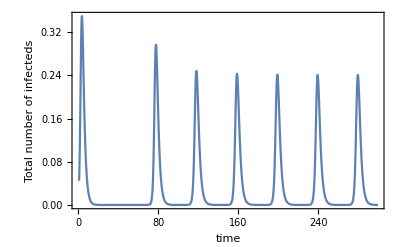

```mathematica
ListLinePlot[Transpose[{tval,IT}],PlotRange->All,Frame->True,FrameLabel->{"time", "Total number of infecteds"}]
```

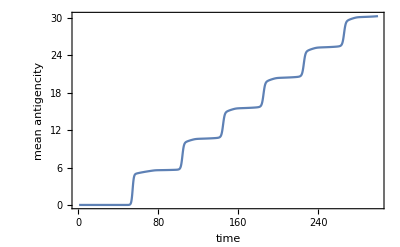

```mathematica
ListLinePlot[Transpose[{tval,ex}],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}]
```

## Oligomorphic dynamics

### Model setting

#### Model parameters

```mathematica
β=2;α=0.1;γ=0.5;S0=1;𝒟=0.001;
```

#### Basic reproductive ratio

```mathematica
ρ=β/(γ+α)S0
```

3.33333

#### Final size of a single epidemic

```mathematica
ψ0=ψ/.FindRoot[ψ==1-Exp[-ρ ψ],{ψ,1-1/ρ}]
```

0.959118

#### Cross immunity function and susceptibility profile after primary outbreak

```mathematica
Clear[x,σ,w];
(* cross-immunity *)
σ[x_]=Exp[-x^2/(2 w^2)];
```

```mathematica
(* susceptibility profile after the first epidemic *)
s[x_]=(1-ψ0)^σ[x];
```

```mathematica
s[x]
```

0.0408823^(ⅇ^(-x^2/(2 w^2)))

```mathematica
ds=D[s[x],x]
```

(3.19706 0.0408823^(ⅇ^(-x^2/(2 w^2))) ⅇ^(-x^2/(2 w^2)) x)/w^2

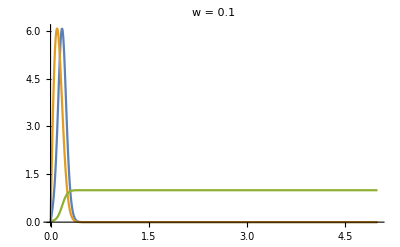

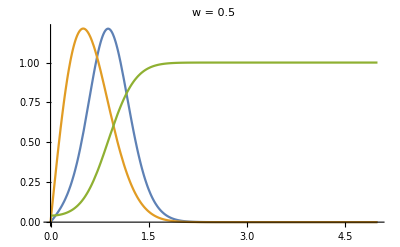

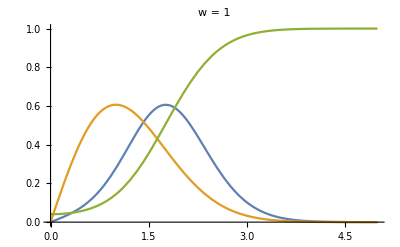

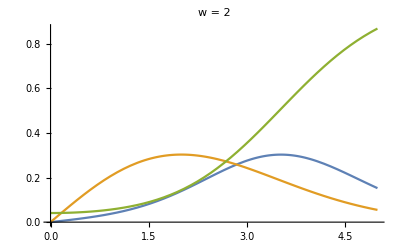

```mathematica
wval=0.1;Plot[Evaluate[{ds,(ⅇ^(-x^2/(2 w^2)) x)/w^2,s[x]}/.w->wval],{x,0,5},PlotLabel->"w = "<>ToString[wval],PlotRange->All]
wval=0.5;Plot[Evaluate[{ds,(ⅇ^(-x^2/(2 w^2)) x)/w^2,s[x]}/.w->wval],{x,0,5},PlotLabel->"w = "<>ToString[wval],PlotRange->All]
wval=1;Plot[Evaluate[{ds,(ⅇ^(-x^2/(2 w^2)) x)/w^2,s[x]}/.w->wval],{x,0,5},PlotLabel->"w = "<>ToString[wval],PlotRange->All]
wval=2;
Plot[Evaluate[{ds,(ⅇ^(-x^2/(2 w^2)) x)/w^2,s[x]}/.w->wval],{x,0,5},PlotLabel->"w = "<>ToString[wval],PlotRange->All]
```

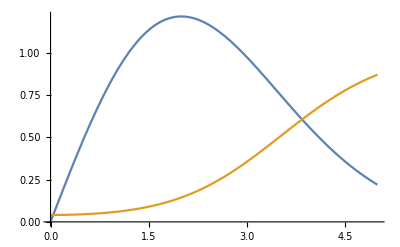

```mathematica
Plot[{ⅇ^(-x^2/(2 w^2)) x/.w->2,s[x]/.w->2},{x,0,5}]
```

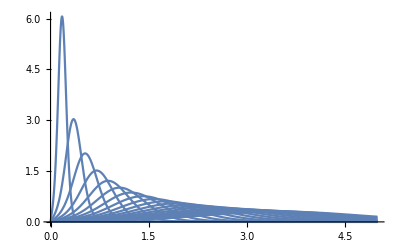

```mathematica
Clear[wval]
Plot[Table[Evaluate[ds/.w->wval],{wval,0.1,2,0.1}],{x,0,5},PlotRange->All,PlotLegends->Automatic]
```

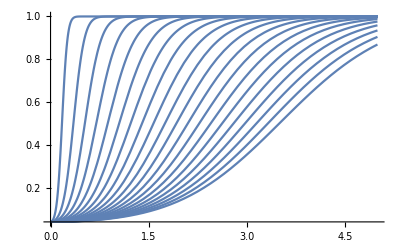

```mathematica
Clear[wval]
Plot[Table[Evaluate[s[x]/.w->wval],{wval,0.1,2,0.1}],{x,0,5},PlotRange->All,PlotLegends->Automatic]
```

#### Model parameters : Cross immunity

```mathematica
w=2;
```

### Constructing OMD for the second outbreak

#### 1. Define susceptibility profile after the first epidemic

```mathematica
(* susceptibility profile after the first epidemic *)
s[x_]=(1-ψ0)^σ[x];
```

#### 2. Obtain the minimum antigenicity distance, xc, necessary to escape the cross - immunity suppression after the first epidemic

```mathematica
(* the minimum antigenicity distance necessary to escape the cross-immunity supression after the first epidemic *)
xc=x/.FindRoot[s[x]==1/ρ,{x,3}]
```

2.79515

### Integrating OMD for the second epidemic outbreak and Compare with simulation results

#### 3. Find the time where the second peak is becoming emerging and set it as the starting point for OMD

#### 4. Divide the antigenicity between two antigenicity groups, those with x < xc and those with x > xc

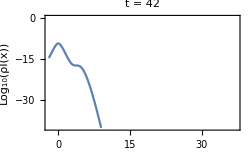

t0 = 42 xc= 2.79515

Sum(I(x),x<xc)= 1.59708×10^-9	Sum(I(x),x>xc)= 5.69458×10^-17

p0 = 1.	p1 = 3.56563×10^-8

E[x|x<xc] = 4.61×10^-7	E[x|x>xc] = 3.40985

V[x|x<xc] = 0.0955883	V[x|x>xc] = 0.354703

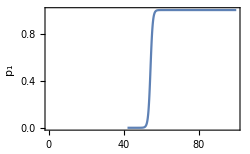

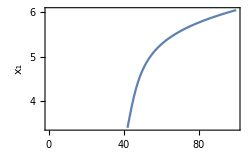

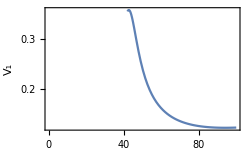

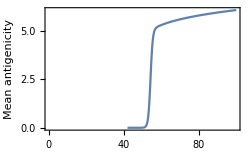

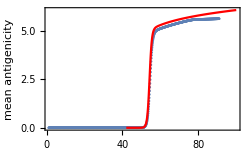

```mathematica
i0=41;
t0=timeTR[[i0]];
ListLinePlot[Transpose[{xval,Log10[ρI⟦i0⟧]}],PlotRange->{-40,0},PlotLabel->"t = "<>ToString[t0],Frame->True,FrameLabel->{"x","Log_10(ρI(x))"},ImageSize->250]

ic=Select[xval,#<xc&]//Length;
(* infected density distribution and antigeniciy traits for x<xc group *)
ρI0=Take[ρI⟦i0⟧,ic];
xval0=Take[xval,ic];
(* infected density distribution and antigeniciy traits for x>xc group *)
ρI1=Take[ρI⟦i0⟧,{ic+1,Length[xval]}];
xval1=Take[xval,{ic+1,Length[xval]}];
(* total infected densities of two groups *)
I0=ρI0//Total;
I1=ρI1//Total;
(* relative proportion of two groups in infected population *)
(* THE INITIAL CONDITION FOR THE 0TH ORDER OMD *)
p0=I0/(I0+I1);
p1=I1/(I0+I1);
(* mean antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 1ST ORDER OMD *)
(* inner product of trait vector and density vector *)
ex0=xval0.ρI0/I0;
ex1=xval1.ρI1/I1;
(* variance of antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 2ND ORDER OMD *)
V0=((xval0-ex0)^2).ρI0/I0;
V1=((xval1-ex1)^2).ρI1/I1;

Print["t0 = ",t0, " xc= ",xc]
Print["Sum(I(x),x<xc)= ",I0, "\tSum(I(x),x>xc)= ",I1]
Print["p0 = ",p0,"\tp1 = ",p1]
Print["E[x|x<xc] = ",ex0,"\tE[x|x>xc] = ",ex1]
Print["V[x|x<xc] = ",V0,"\tV[x|x>xc] = ",V1]

tend=100;
Clear[t,P,M,V]
ser=NDSolve[{
P'[t]==β (s[M[t]]-s[ex0])P[t](1-P[t]),
M'[t]==β s'[M[t]]V[t],
V'[t]==β s''[M[t]]V[t]^2+2𝒟,
P[t0]==p1,
M[t0]==ex1,
V[t0]==V1},
{P,M,V},{t,t0,tend}];
(* Frequency of morph 1 *)
Plot[P[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","p_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}]
(* Mean antigenicity of morph 1 *)
Plot[M[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","x_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}]
(* Variance in morph 1 *)
Plot[V[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","V_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}]
(* Mean antigenicity of the population *)
Plot[((1-P[t])ex0+P[t]M[t])/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","Mean antigenicity"},ImageSize->250,PlotRange->{{0,tend},Automatic}]
grfA=Show[
ListPlot[Take[Transpose[{tval,ex}],900],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}],
(* ListLinePlot[Transpose[{tser,ex1ser}],PlotStyle->{Dashed,Red}], *)
Plot[((1-P[t])ex0+P[t]M[t])/.ser,{t,t0,tend},PlotRange->All,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"t","mean antigenicity"},Axes->None,ImageSize->250
]
```

## Varying prediction timing

```mathematica
i0ser=Range[1,50]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

t0 = 2 xc= 2.79515

Sum(I(x),x<xc)= 0.130032	Sum(I(x),x>xc)= 5.12668×10^-31

p0 = 1.	p1 = 3.94263×10^-30

E[x|x<xc] = 5.2442×10^-19	E[x|x>xc] = 2.80062

V[x|x<xc] = 0.00397265	V[x|x>xc] = 0.000124828

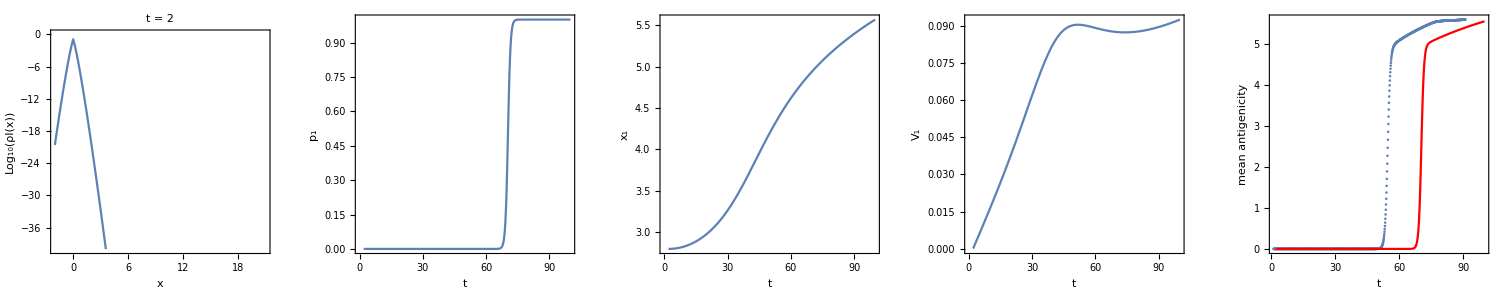

t0 = 3 xc= 2.79515

Sum(I(x),x<xc)= 0.283699	Sum(I(x),x>xc)= 4.58786×10^-28

p0 = 1.	p1 = 1.61716×10^-27

E[x|x<xc] = 1.13309×10^-18	E[x|x>xc] = 2.80098

V[x|x<xc] = 0.00597289	V[x|x>xc] = 0.000197286

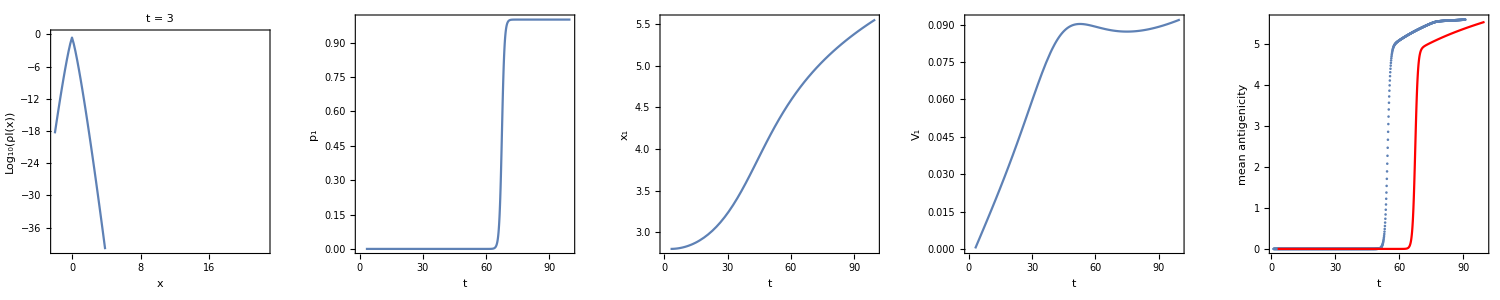

t0 = 4 xc= 2.79515

Sum(I(x),x<xc)= 0.348986	Sum(I(x),x>xc)= 4.82316×10^-26

p0 = 1.	p1 = 1.38205×10^-25

E[x|x<xc] = 7.6421×10^-19	E[x|x>xc] = 2.8014

V[x|x<xc] = 0.00800265	V[x|x>xc] = 0.000280736

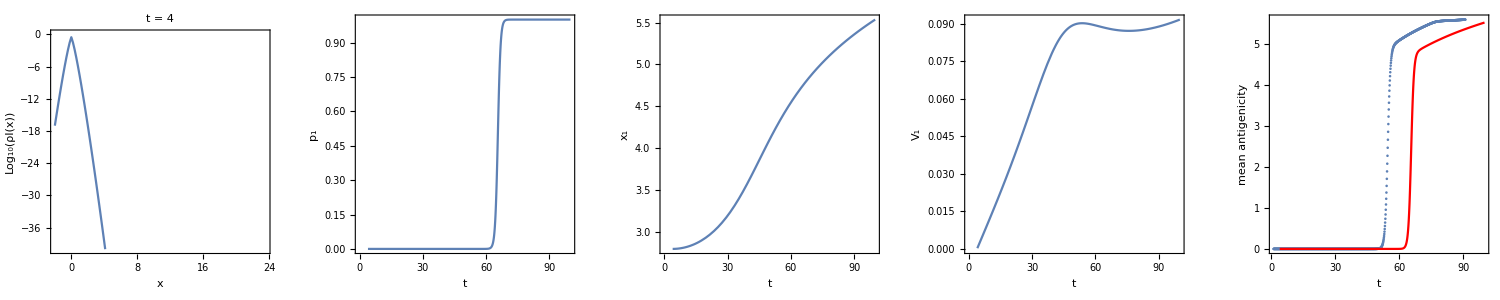

t0 = 5 xc= 2.79515

Sum(I(x),x<xc)= 0.288492	Sum(I(x),x>xc)= 1.31609×10^-24

p0 = 1.	p1 = 4.56196×10^-24

E[x|x<xc] = 8.7691×10^-19	E[x|x>xc] = 2.80187

V[x|x<xc] = 0.0100488	V[x|x>xc] = 0.000376933

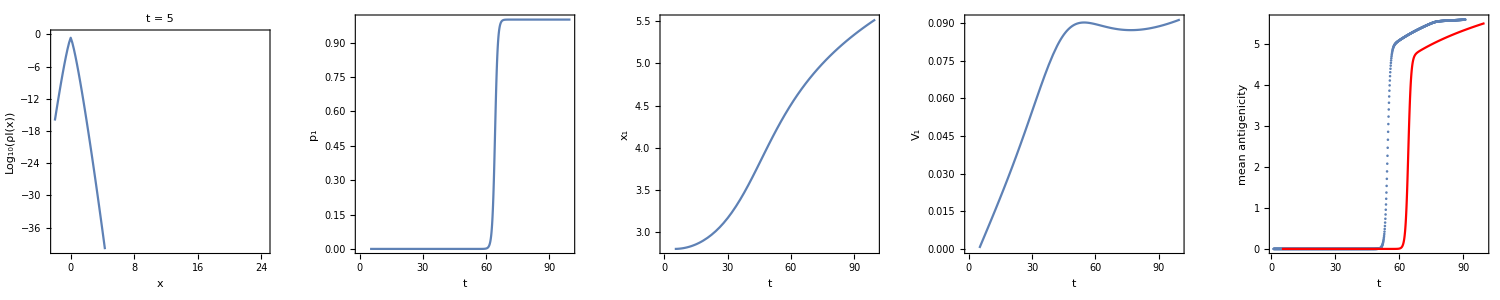

t0 = 6 xc= 2.79515

Sum(I(x),x<xc)= 0.198845	Sum(I(x),x>xc)= 1.51905×10^-23

p0 = 1.	p1 = 7.63938×10^-23

E[x|x<xc] = 8.48859×10^-18	E[x|x>xc] = 2.80239

V[x|x<xc] = 0.0120993	V[x|x>xc] = 0.000483329

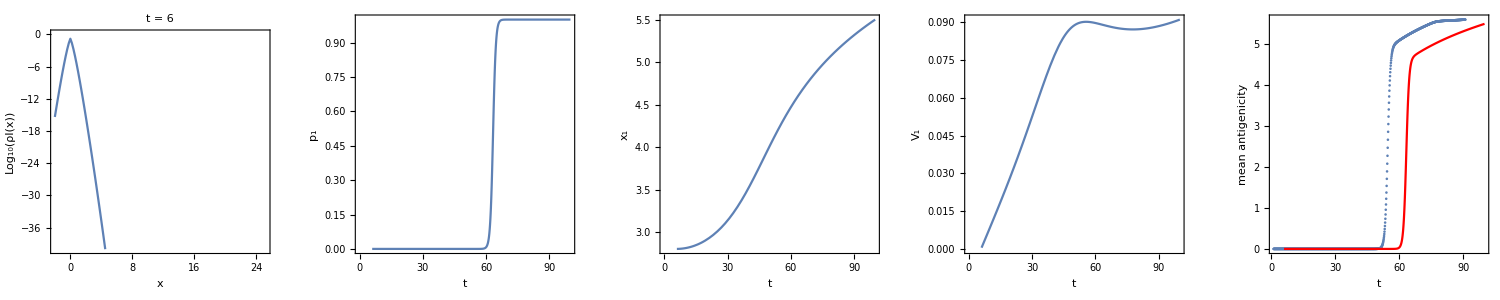

t0 = 7 xc= 2.79515

Sum(I(x),x<xc)= 0.126885	Sum(I(x),x>xc)= 1.00876×10^-22

p0 = 1.	p1 = 7.9502×10^-22

E[x|x<xc] = 5.60799×10^-17	E[x|x>xc] = 2.80295

V[x|x<xc] = 0.0141519	V[x|x>xc] = 0.000597797

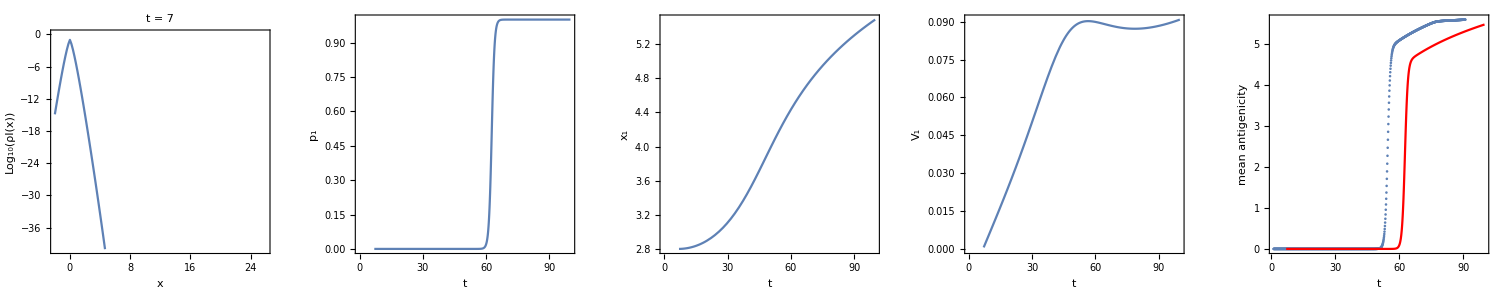

t0 = 8 xc= 2.79515

Sum(I(x),x<xc)= 0.0781682	Sum(I(x),x>xc)= 4.62566×10^-22

p0 = 1.	p1 = 5.91758×10^-21

E[x|x<xc] = 2.62388×10^-16	E[x|x>xc] = 2.80354

V[x|x<xc] = 0.0162073	V[x|x>xc] = 0.00071982

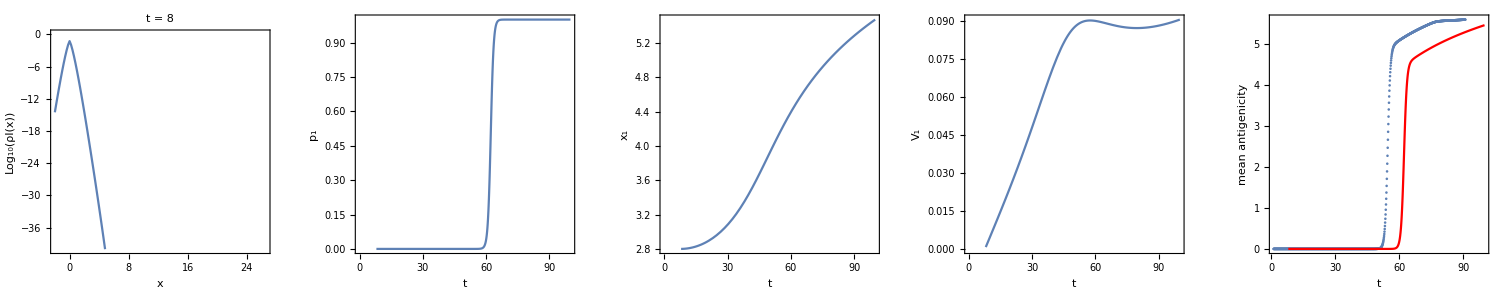

t0 = 9 xc= 2.79515

Sum(I(x),x<xc)= 0.0473213	Sum(I(x),x>xc)= 1.63371×10^-21

p0 = 1.	p1 = 3.45238×10^-20

E[x|x<xc] = 1.023×10^-15	E[x|x>xc] = 2.80417

V[x|x<xc] = 0.0182671	V[x|x>xc] = 0.000849936

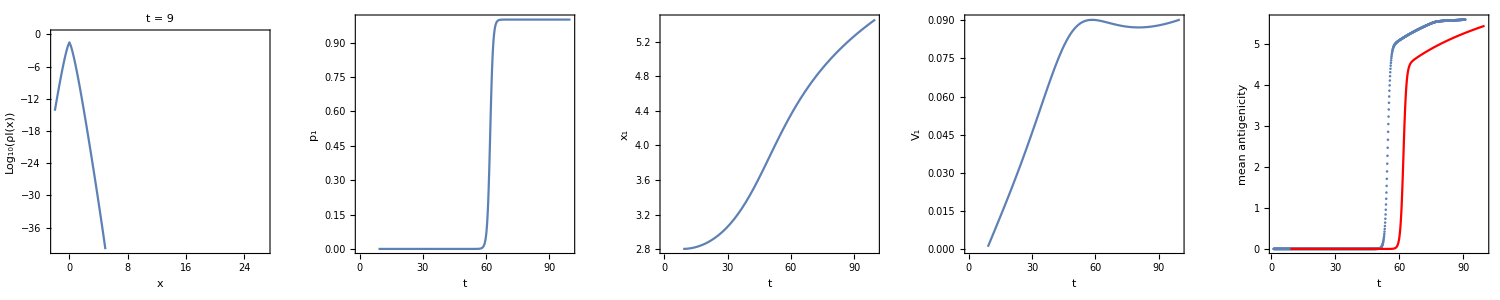

t0 = 10 xc= 2.79515

Sum(I(x),x<xc)= 0.0283832	Sum(I(x),x>xc)= 4.75756×10^-21

p0 = 1.	p1 = 1.67619×10^-19

E[x|x<xc] = 3.46895×10^-15	E[x|x>xc] = 2.80484

V[x|x<xc] = 0.0203327	V[x|x>xc] = 0.000989228

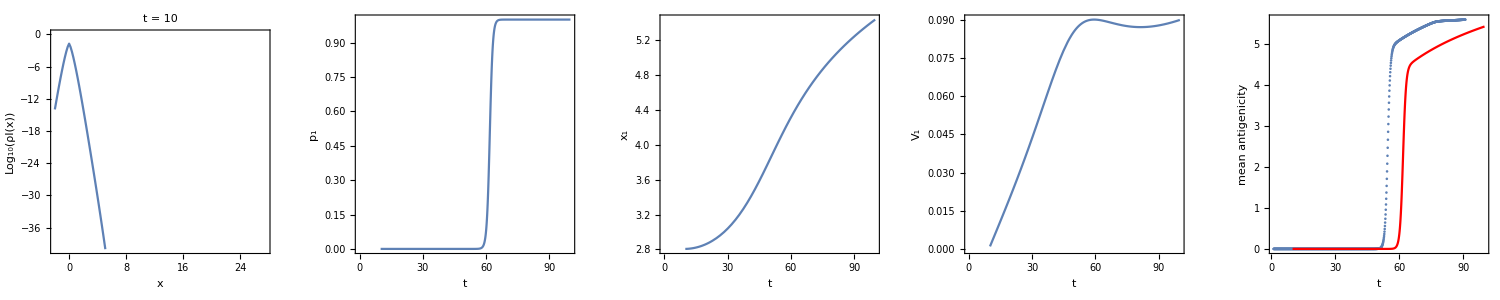

t0 = 11 xc= 2.79515

Sum(I(x),x<xc)= 0.0169374	Sum(I(x),x>xc)= 1.19441×10^-20

p0 = 1.	p1 = 7.05188×10^-19

E[x|x<xc] = 1.05691×10^-14	E[x|x>xc] = 2.80555

V[x|x<xc] = 0.0224053	V[x|x>xc] = 0.00113907

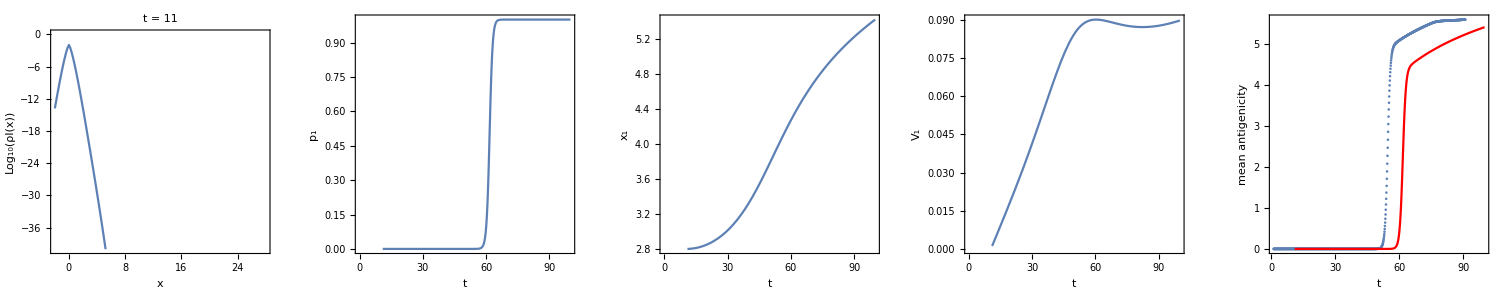

t0 = 12 xc= 2.79515

Sum(I(x),x<xc)= 0.0100782	Sum(I(x),x>xc)= 2.66512×10^-20

p0 = 1.	p1 = 2.64443×10^-18

E[x|x<xc] = 2.94044×10^-14	E[x|x>xc] = 2.80631

V[x|x<xc] = 0.024486	V[x|x>xc] = 0.00130104

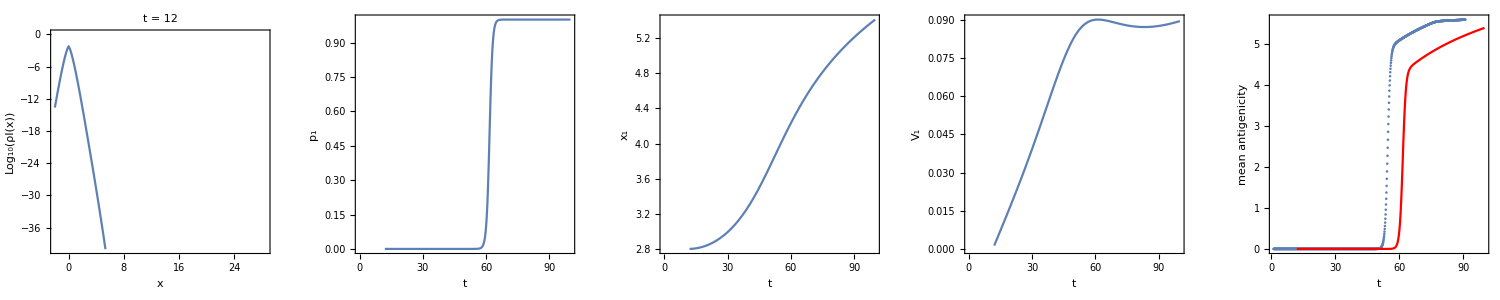

t0 = 13 xc= 2.79515

Sum(I(x),x<xc)= 0.00598702	Sum(I(x),x>xc)= 5.40134×10^-20

p0 = 1.	p1 = 9.02175×10^-18

E[x|x<xc] = 7.60326×10^-14	E[x|x>xc] = 2.80714

V[x|x<xc] = 0.0265758	V[x|x>xc] = 0.00147691

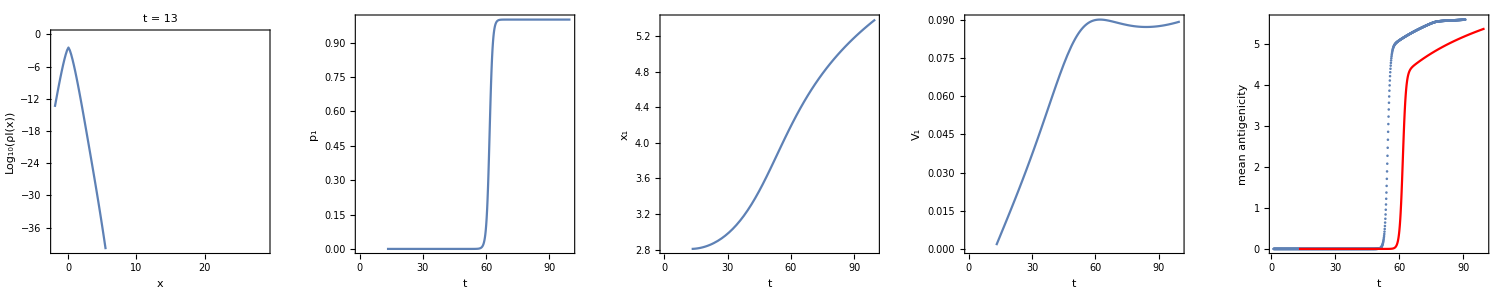

t0 = 14 xc= 2.79515

Sum(I(x),x<xc)= 0.00355332	Sum(I(x),x>xc)= 1.01035×10^-19

p0 = 1.	p1 = 2.84339×10^-17

E[x|x<xc] = 1.84549×10^-13	E[x|x>xc] = 2.80803

V[x|x<xc] = 0.0286756	V[x|x>xc] = 0.00166869

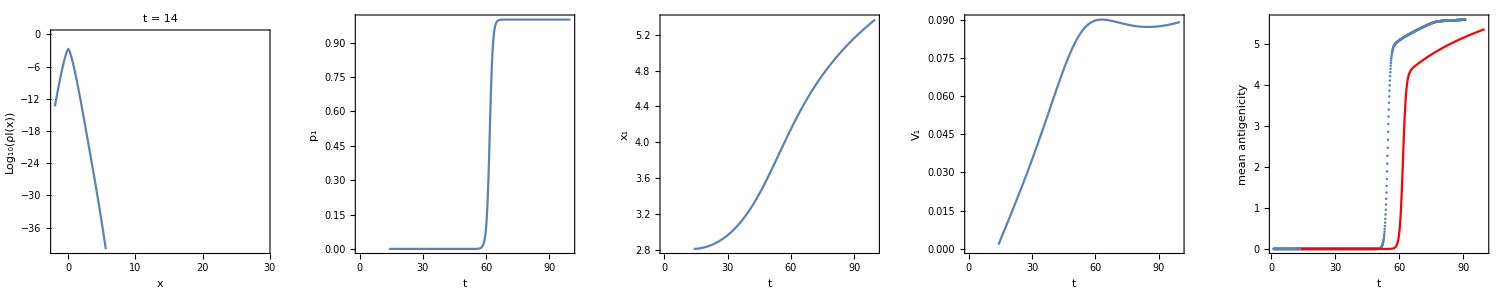

t0 = 15 xc= 2.79515

Sum(I(x),x<xc)= 0.00210782	Sum(I(x),x>xc)= 1.76575×10^-19

p0 = 1.	p1 = 8.37716×10^-17

E[x|x<xc] = 4.24633×10^-13	E[x|x>xc] = 2.80899

V[x|x<xc] = 0.0307864	V[x|x>xc] = 0.00187867

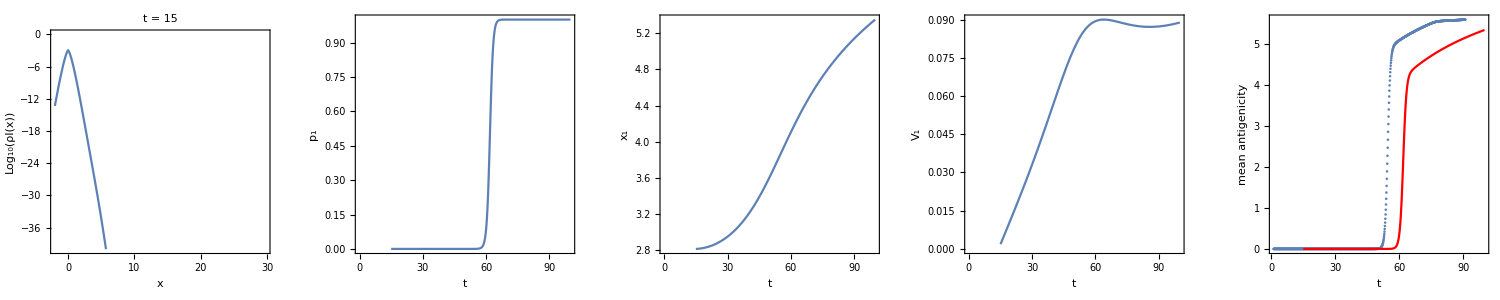

t0 = 16 xc= 2.79515

Sum(I(x),x<xc)= 0.00125001	Sum(I(x),x>xc)= 2.91093×10^-19

p0 = 1.	p1 = 2.32874×10^-16

E[x|x<xc] = 9.3231×10^-13	E[x|x>xc] = 2.81004

V[x|x<xc] = 0.0329089	V[x|x>xc] = 0.00210949

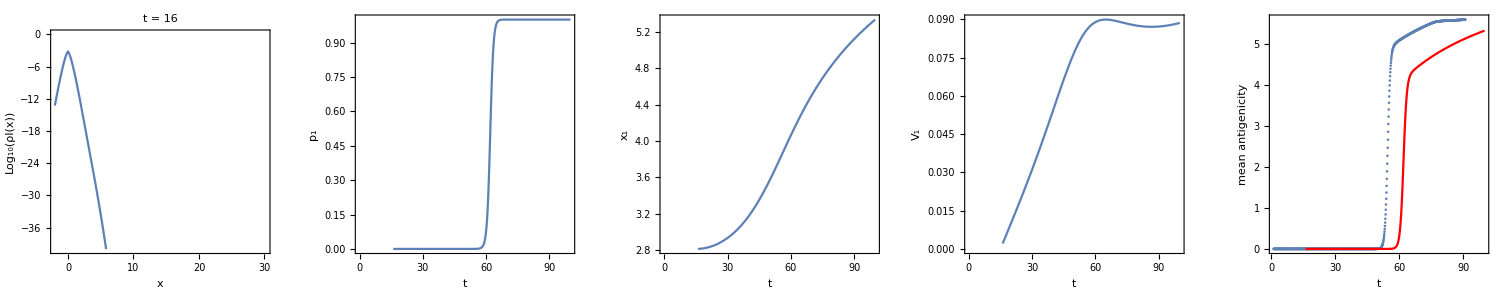

t0 = 17 xc= 2.79515

Sum(I(x),x<xc)= 0.000741195	Sum(I(x),x>xc)= 4.56152×10^-19

p0 = 1.	p1 = 6.15428×10^-16

E[x|x<xc] = 1.94429×10^-12	E[x|x>xc] = 2.81118

V[x|x<xc] = 0.035044	V[x|x>xc] = 0.00236425

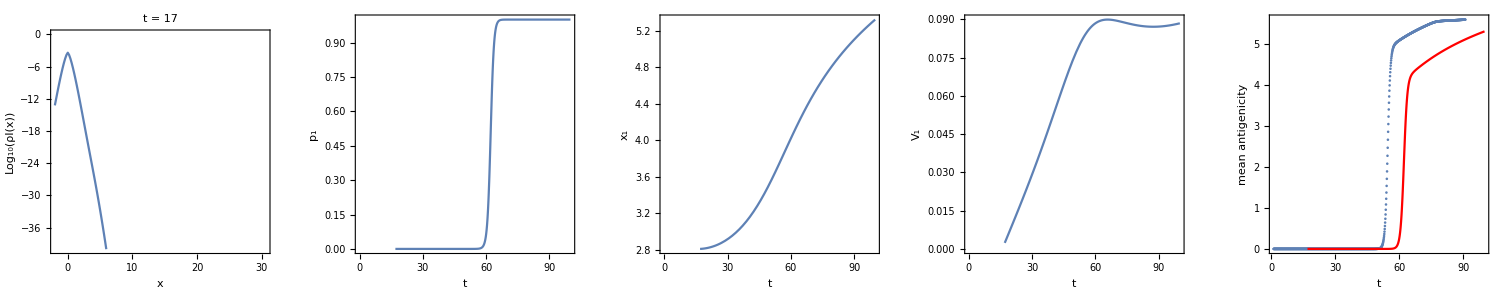

t0 = 18 xc= 2.79515

Sum(I(x),x<xc)= 0.000439472	Sum(I(x),x>xc)= 6.83733×10^-19

p0 = 1.	p1 = 1.5558×10^-15

E[x|x<xc] = 3.95577×10^-12	E[x|x>xc] = 2.81243

V[x|x<xc] = 0.0371925	V[x|x>xc] = 0.00264663

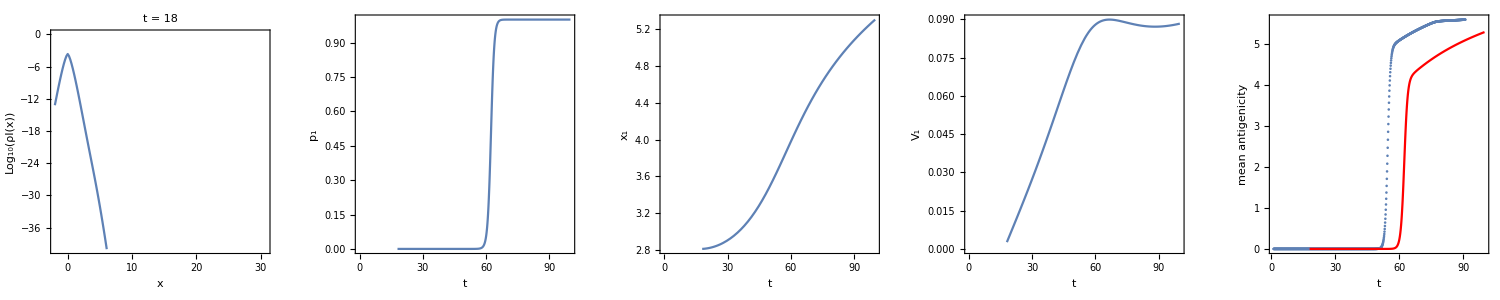

t0 = 19 xc= 2.79515

Sum(I(x),x<xc)= 0.000260574	Sum(I(x),x>xc)= 9.8544×10^-19

p0 = 1.	p1 = 3.78181×10^-15

E[x|x<xc] = 7.85452×10^-12	E[x|x>xc] = 2.8138

V[x|x<xc] = 0.0393554	V[x|x>xc] = 0.00296103

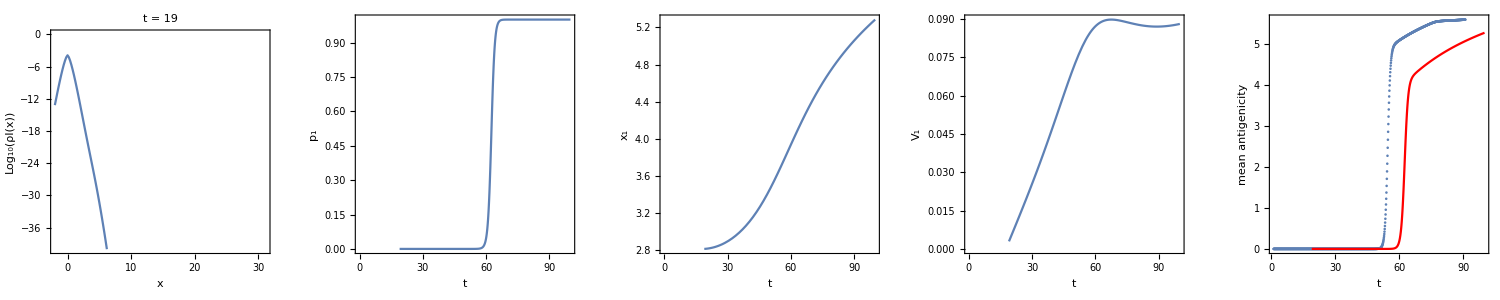

t0 = 20 xc= 2.79515

Sum(I(x),x<xc)= 0.000154505	Sum(I(x),x>xc)= 1.37169×10^-18

p0 = 1.	p1 = 8.87798×10^-15

E[x|x<xc] = 1.50126×10^-11	E[x|x>xc] = 2.8153

V[x|x<xc] = 0.0415334	V[x|x>xc] = 0.0033128

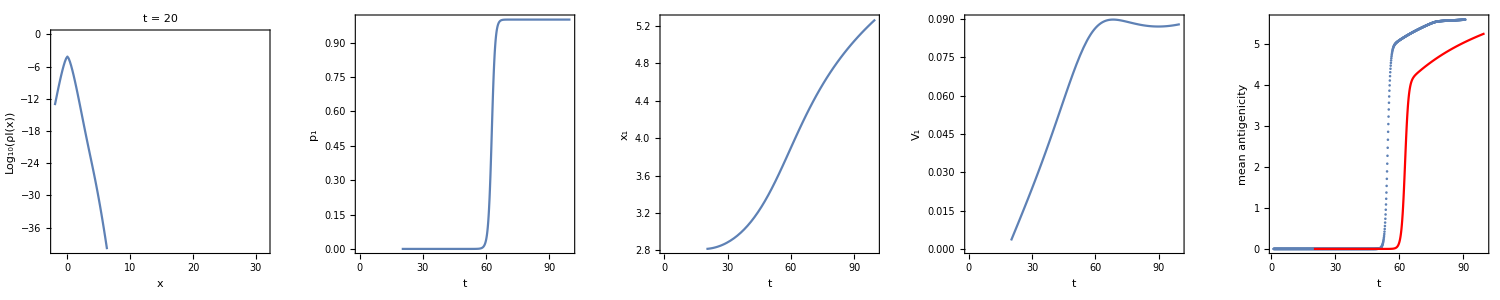

t0 = 21 xc= 2.79515

Sum(I(x),x<xc)= 0.0000916166	Sum(I(x),x>xc)= 1.85099×10^-18

p0 = 1.	p1 = 2.02036×10^-14

E[x|x<xc] = 2.77754×10^-11	E[x|x>xc] = 2.81696

V[x|x<xc] = 0.0437275	V[x|x>xc] = 0.00370847

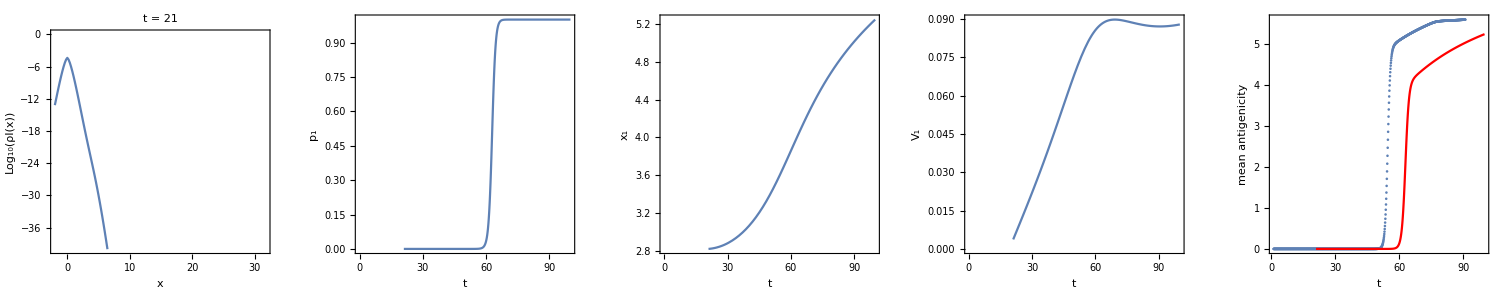

t0 = 22 xc= 2.79515

Sum(I(x),x<xc)= 0.000054329	Sum(I(x),x>xc)= 2.42936×10^-18

p0 = 1.	p1 = 4.47157×10^-14

E[x|x<xc] = 5.05621×10^-11	E[x|x>xc] = 2.8188

V[x|x<xc] = 0.0459386	V[x|x>xc] = 0.00415617

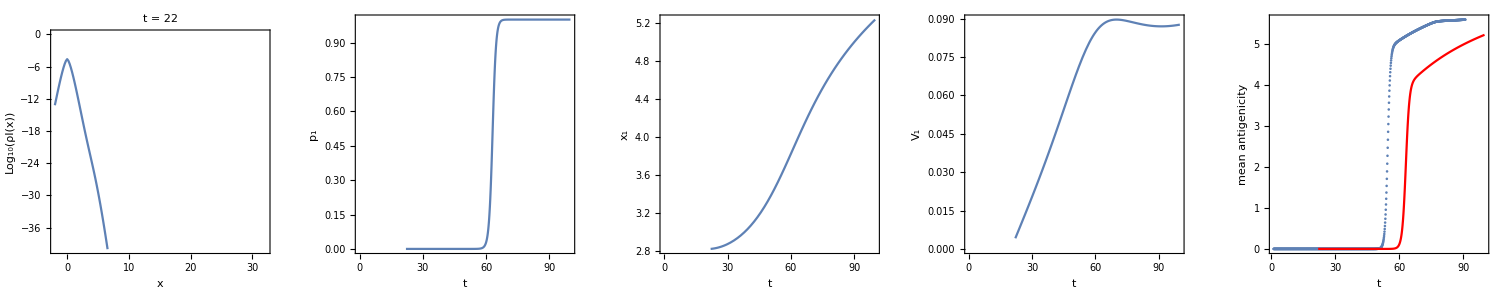

t0 = 23 xc= 2.79515

Sum(I(x),x<xc)= 0.0000322194	Sum(I(x),x>xc)= 3.11002×10^-18

p0 = 1.	p1 = 9.65261×10^-14

E[x|x<xc] = 8.99613×10^-11	E[x|x>xc] = 2.82085

V[x|x<xc] = 0.0481677	V[x|x>xc] = 0.00466611

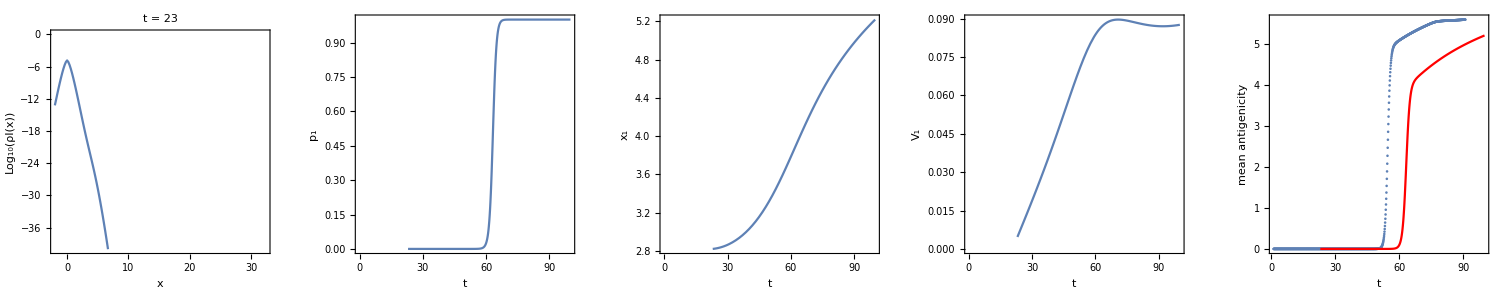

t0 = 24 xc= 2.79515

Sum(I(x),x<xc)= 0.0000191088	Sum(I(x),x>xc)= 3.89327×10^-18

p0 = 1.	p1 = 2.03742×10^-13

E[x|x<xc] = 1.57037×10^-10	E[x|x>xc] = 2.82314

V[x|x<xc] = 0.0504156	V[x|x>xc] = 0.00525131

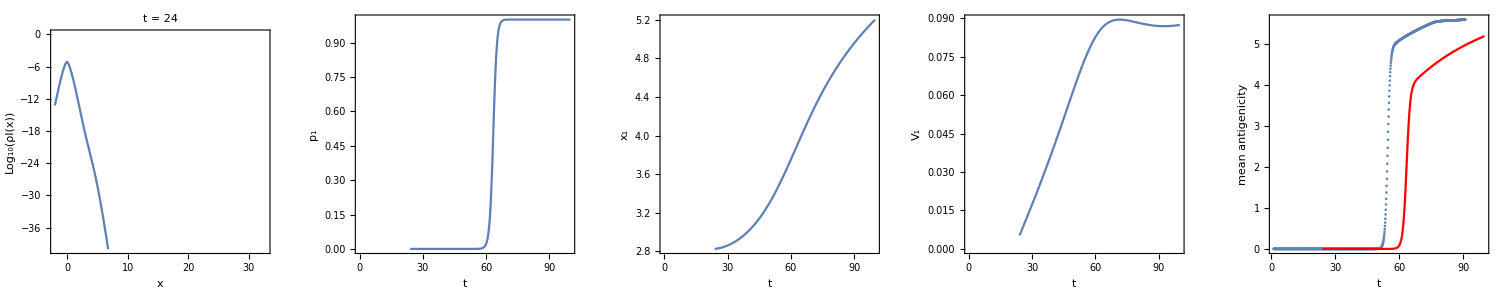

t0 = 25 xc= 2.79515

Sum(I(x),x<xc)= 0.000011334	Sum(I(x),x>xc)= 4.77673×10^-18

p0 = 1.	p1 = 4.21453×10^-13

E[x|x<xc] = 2.69082×10^-10	E[x|x>xc] = 2.82571

V[x|x<xc] = 0.0526836	V[x|x>xc] = 0.00592862

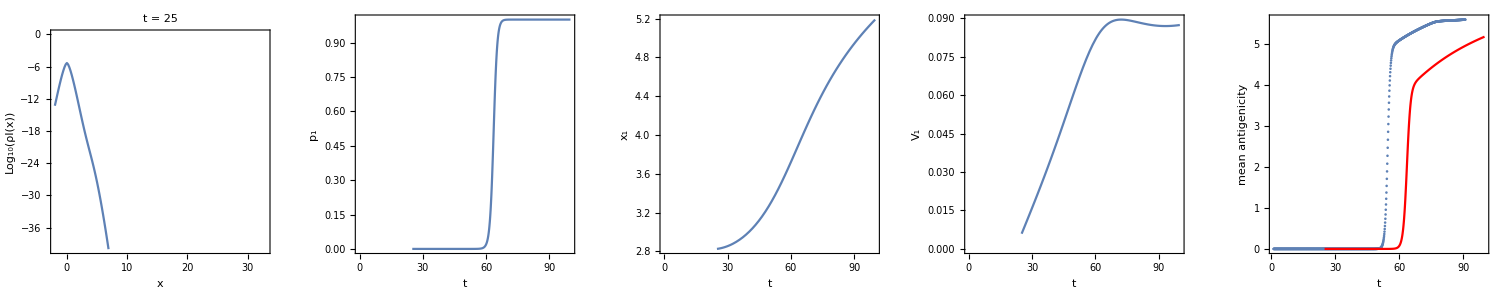

t0 = 26 xc= 2.79515

Sum(I(x),x<xc)= 6.72298×10^-6	Sum(I(x),x>xc)= 5.7557×10^-18

p0 = 1.	p1 = 8.56124×10^-13

E[x|x<xc] = 4.53771×10^-10	E[x|x>xc] = 2.82861

V[x|x<xc] = 0.0549726	V[x|x>xc] = 0.00672027

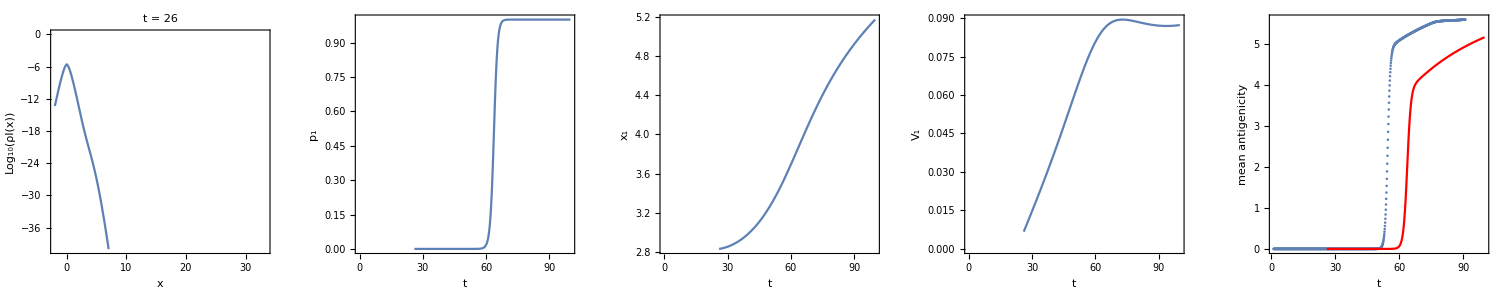

t0 = 27 xc= 2.79515

Sum(I(x),x<xc)= 3.98818×10^-6	Sum(I(x),x>xc)= 6.82383×10^-18

p0 = 1.	p1 = 1.71101×10^-12

E[x|x<xc] = 7.53395×10^-10	E[x|x>xc] = 2.83191

V[x|x<xc] = 0.0572838	V[x|x>xc] = 0.00765611

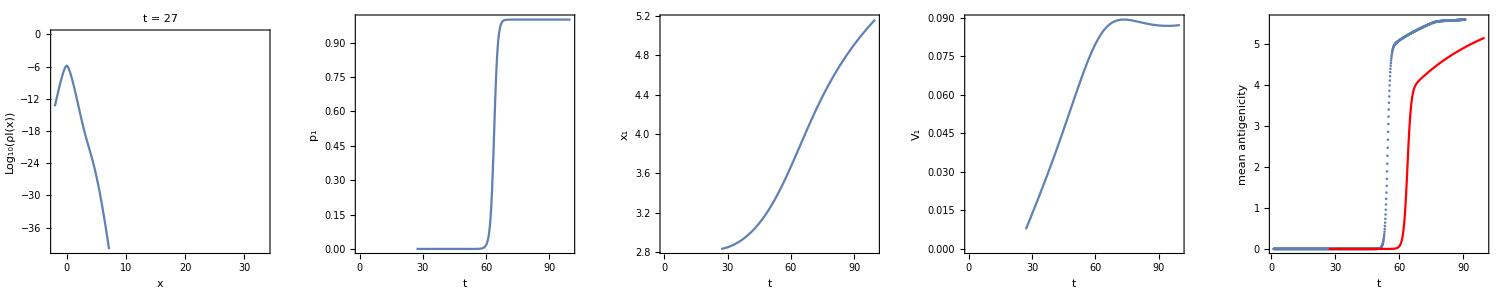

t0 = 28 xc= 2.79515

Sum(I(x),x<xc)= 2.36604×10^-6	Sum(I(x),x>xc)= 7.97395×10^-18

p0 = 1.	p1 = 3.37017×10^-12

E[x|x<xc] = 1.23405×10^-9	E[x|x>xc] = 2.83569

V[x|x<xc] = 0.0596184	V[x|x>xc] = 0.00877715

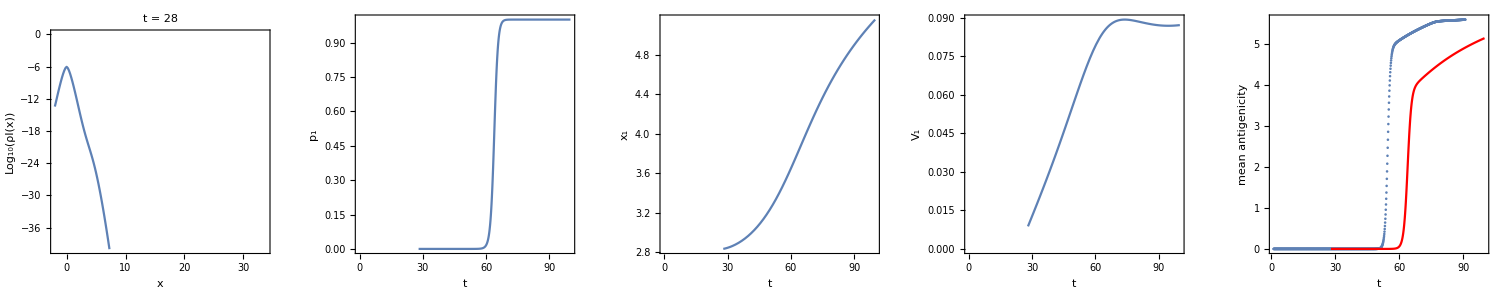

t0 = 29 xc= 2.79515

Sum(I(x),x<xc)= 1.40379×10^-6	Sum(I(x),x>xc)= 9.19907×10^-18

p0 = 1.	p1 = 6.55301×10^-12

E[x|x<xc] = 1.98653×10^-9	E[x|x>xc] = 2.84006

V[x|x<xc] = 0.0619775	V[x|x>xc] = 0.010141

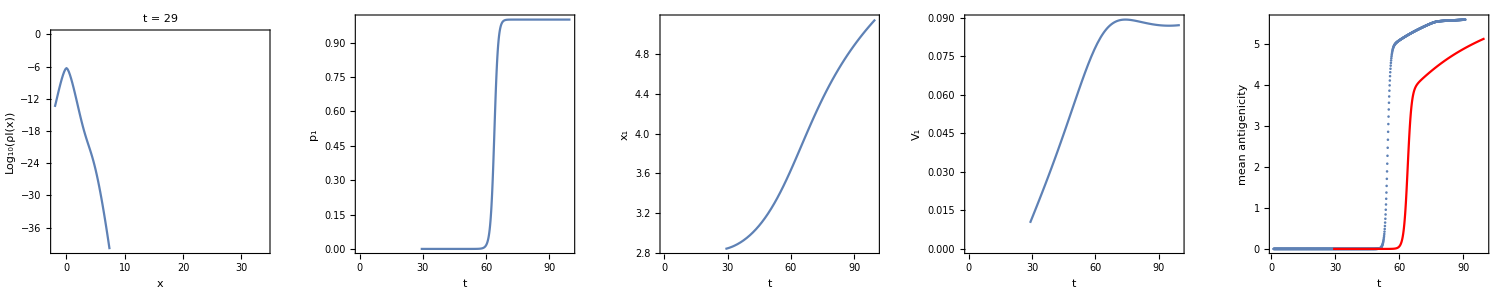

t0 = 30 xc= 2.79515

Sum(I(x),x<xc)= 8.3295×10^-7	Sum(I(x),x>xc)= 1.04935×10^-17

p0 = 1.	p1 = 1.25981×10^-11

E[x|x<xc] = 3.19033×10^-9	E[x|x>xc] = 2.84517

V[x|x<xc] = 0.0643626	V[x|x>xc] = 0.0118309

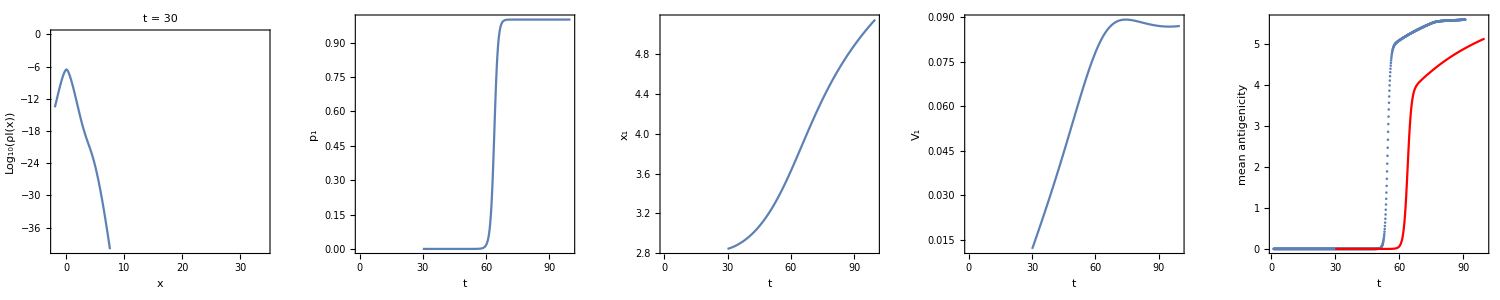

t0 = 31 xc= 2.79515

Sum(I(x),x<xc)= 4.94277×10^-7	Sum(I(x),x>xc)= 1.18545×10^-17

p0 = 1.	p1 = 2.39836×10^-11

E[x|x<xc] = 5.04245×10^-9	E[x|x>xc] = 2.85121

V[x|x<xc] = 0.0667749	V[x|x>xc] = 0.0139702

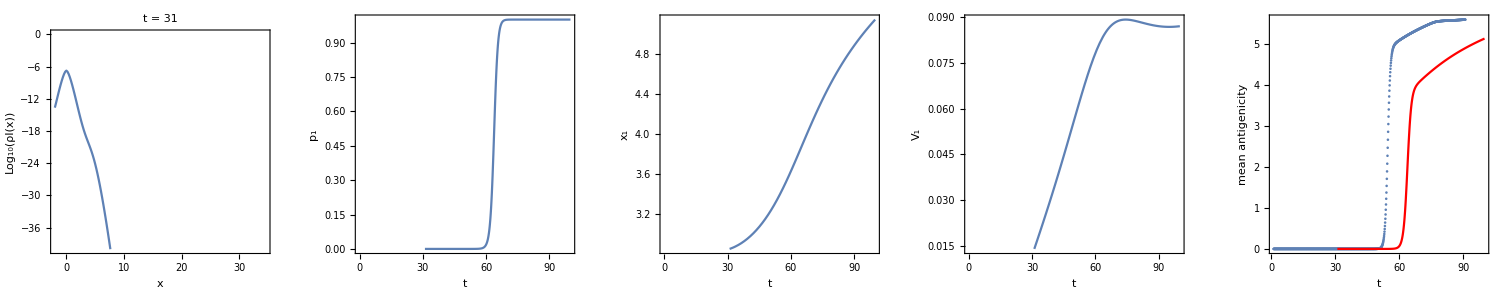

t0 = 32 xc= 2.79515

Sum(I(x),x<xc)= 2.9333×10^-7	Sum(I(x),x>xc)= 1.32837×10^-17

p0 = 1.	p1 = 4.52857×10^-11

E[x|x<xc] = 7.8971×10^-9	E[x|x>xc] = 2.85848

V[x|x<xc] = 0.0692159	V[x|x>xc] = 0.0167473

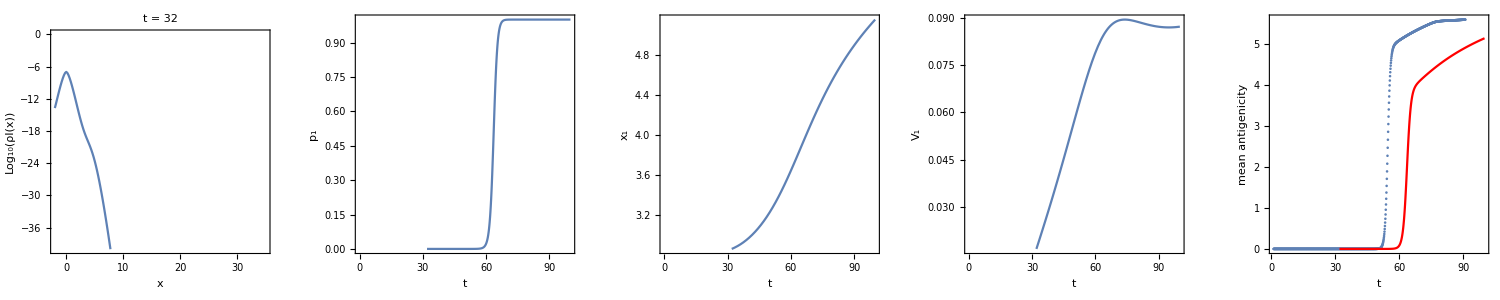

t0 = 33 xc= 2.79515

Sum(I(x),x<xc)= 1.74093×10^-7	Sum(I(x),x>xc)= 1.47898×10^-17

p0 = 1.	p1 = 8.49538×10^-11

E[x|x<xc] = 1.22455×10^-8	E[x|x>xc] = 2.8674

V[x|x<xc] = 0.0716871	V[x|x>xc] = 0.0204584

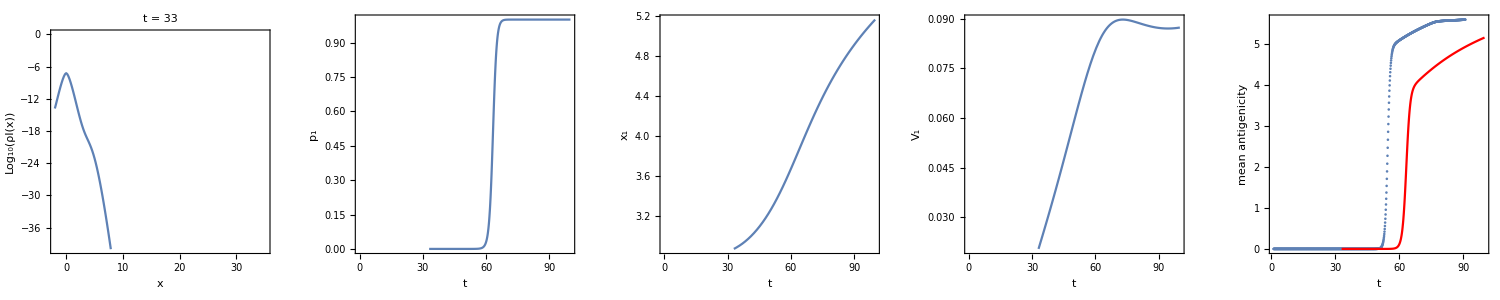

t0 = 34 xc= 2.79515

Sum(I(x),x<xc)= 1.03333×10^-7	Sum(I(x),x>xc)= 1.63925×10^-17

p0 = 1.	p1 = 1.58637×10^-10

E[x|x<xc] = 1.8824×10^-8	E[x|x>xc] = 2.87858

V[x|x<xc] = 0.0741901	V[x|x>xc] = 0.0255822

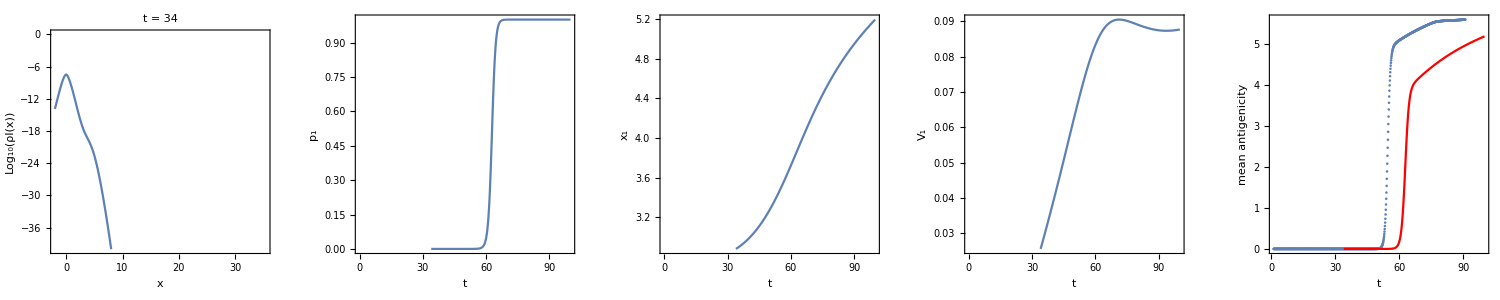

t0 = 35 xc= 2.79515

Sum(I(x),x<xc)= 6.13392×10^-8	Sum(I(x),x>xc)= 1.81281×10^-17

p0 = 1.	p1 = 2.95539×10^-10

E[x|x<xc] = 2.87087×10^-8	E[x|x>xc] = 2.89302

V[x|x<xc] = 0.0767267	V[x|x>xc] = 0.0329104

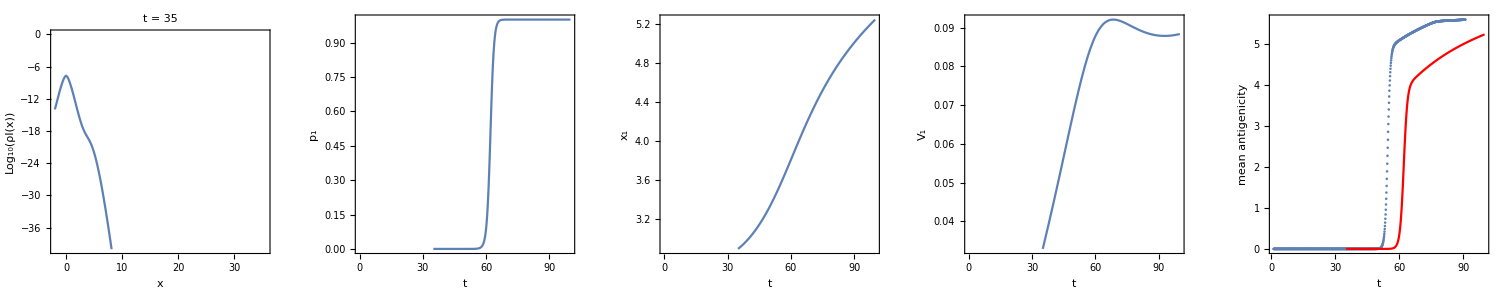

t0 = 36 xc= 2.79515

Sum(I(x),x<xc)= 3.64145×10^-8	Sum(I(x),x>xc)= 2.00612×10^-17

p0 = 1.	p1 = 5.50914×10^-10

E[x|x<xc] = 4.3419×10^-8	E[x|x>xc] = 2.91225

V[x|x<xc] = 0.0792985	V[x|x>xc] = 0.043769

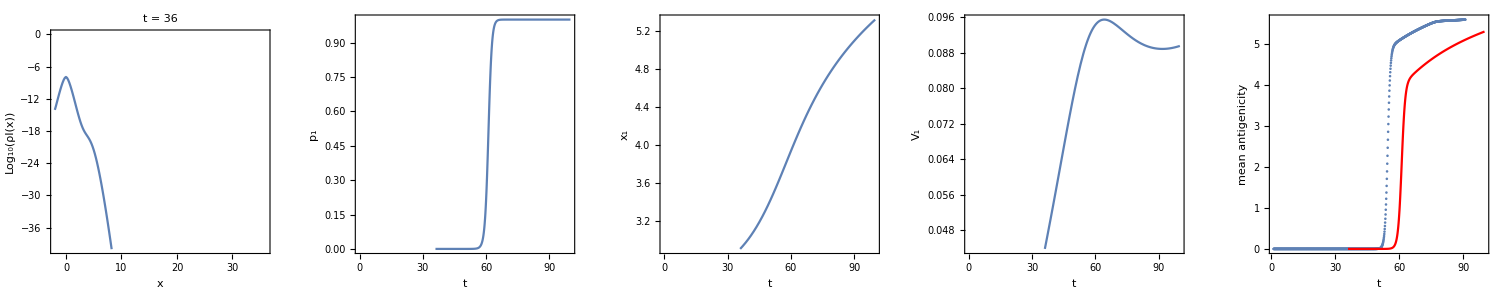

t0 = 37 xc= 2.79515

Sum(I(x),x<xc)= 2.16196×10^-8	Sum(I(x),x>xc)= 2.23045×10^-17

p0 = 1.	p1 = 1.03168×10^-9

E[x|x<xc] = 6.53363×10^-8	E[x|x>xc] = 2.93881

V[x|x<xc] = 0.0819076	V[x|x>xc] = 0.0603699

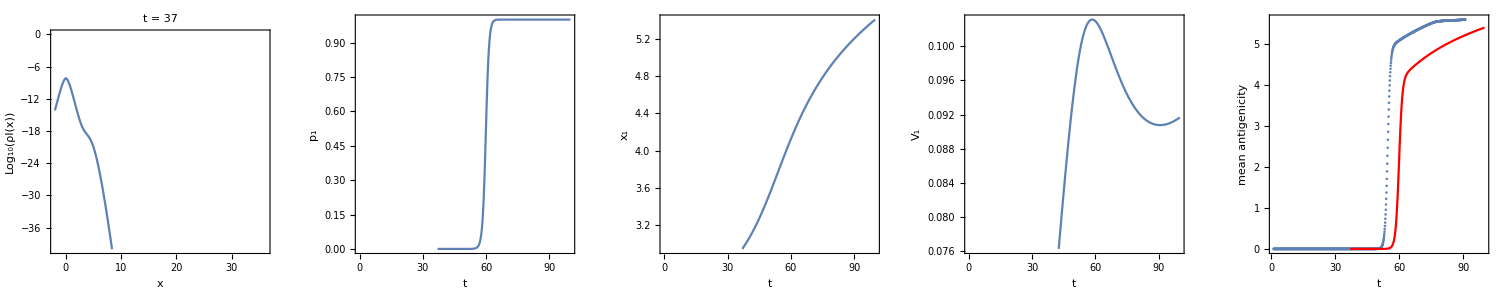

t0 = 38 xc= 2.79515

Sum(I(x),x<xc)= 1.2837×10^-8	Sum(I(x),x>xc)= 2.50596×10^-17

p0 = 1.	p1 = 1.95215×10^-9

E[x|x<xc] = 9.75849×10^-8	E[x|x>xc] = 2.97682

V[x|x<xc] = 0.0845559	V[x|x>xc] = 0.0862635

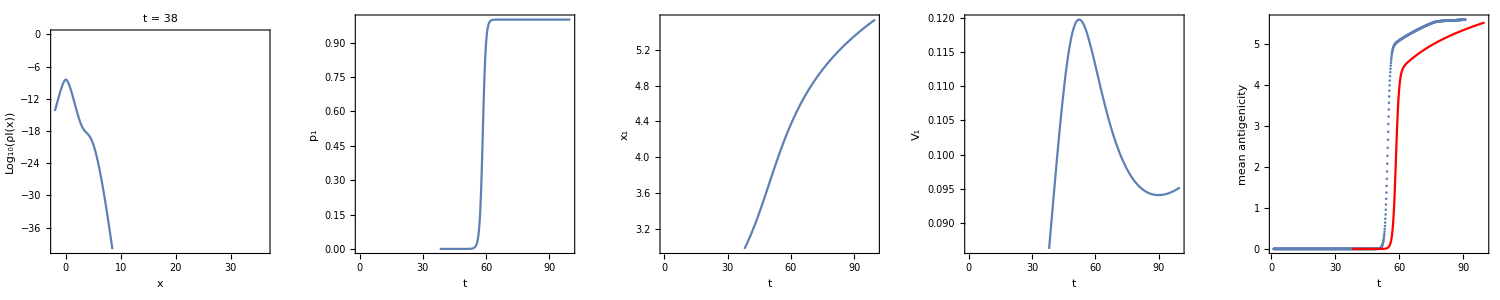

t0 = 39 xc= 2.79515

Sum(I(x),x<xc)= 7.62282×10^-9	Sum(I(x),x>xc)= 2.87012×10^-17

p0 = 1.	p1 = 3.76517×10^-9

E[x|x<xc] = 1.44964×10^-7	E[x|x>xc] = 3.03286

V[x|x<xc] = 0.0872457	V[x|x>xc] = 0.126564

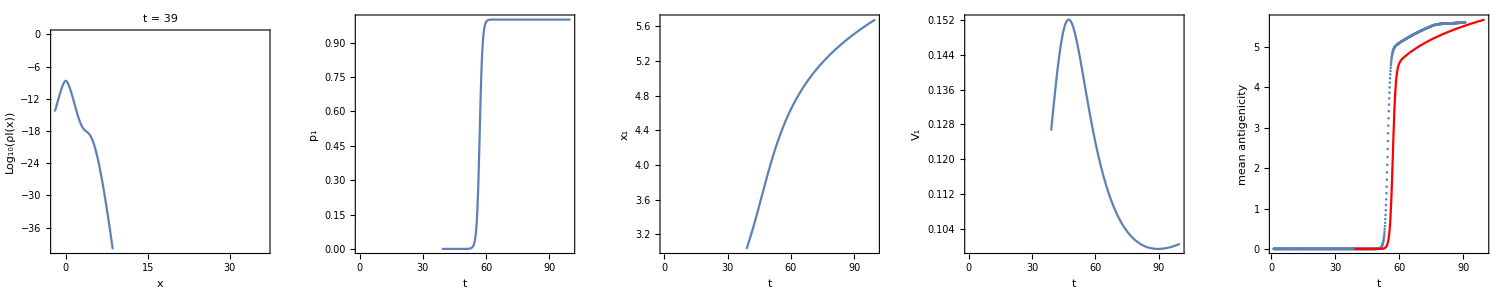

t0 = 40 xc= 2.79515

Sum(I(x),x<xc)= 4.527×10^-9	Sum(I(x),x>xc)= 3.39571×10^-17

p0 = 1.	p1 = 7.50101×10^-9

E[x|x<xc] = 2.1419×10^-7	E[x|x>xc] = 3.11653

V[x|x<xc] = 0.0899794	V[x|x>xc] = 0.186751

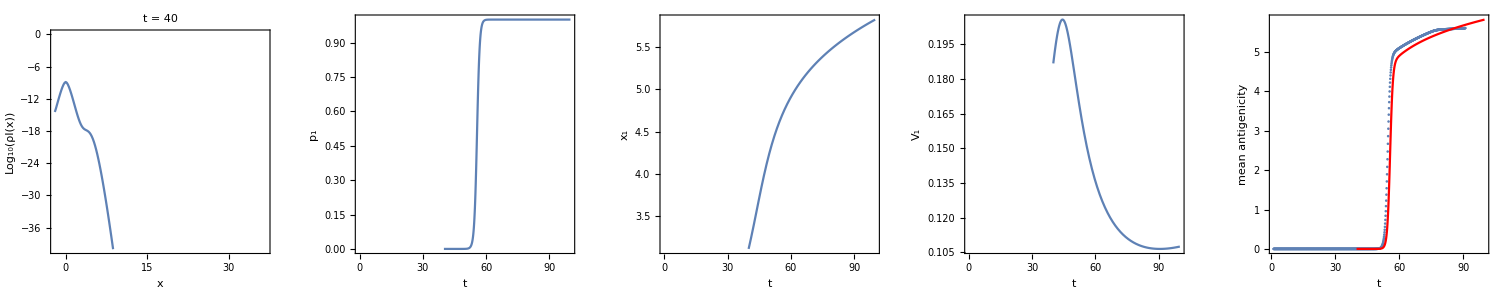

t0 = 41 xc= 2.79515

Sum(I(x),x<xc)= 2.68873×10^-9	Sum(I(x),x>xc)= 4.23125×10^-17

p0 = 1.	p1 = 1.5737×10^-8

E[x|x<xc] = 3.14883×10^-7	E[x|x>xc] = 3.23948

V[x|x<xc] = 0.0927593	V[x|x>xc] = 0.267511

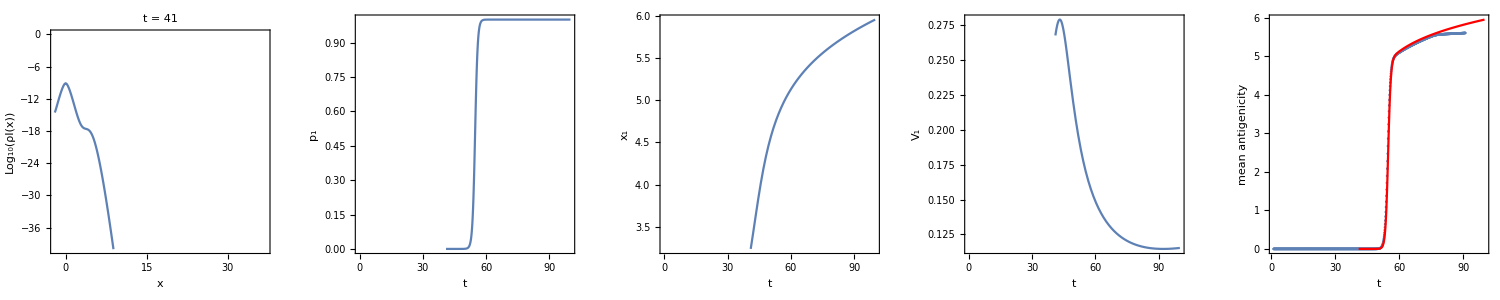

t0 = 42 xc= 2.79515

Sum(I(x),x<xc)= 1.59708×10^-9	Sum(I(x),x>xc)= 5.69458×10^-17

p0 = 1.	p1 = 3.56563×10^-8

E[x|x<xc] = 4.61×10^-7	E[x|x>xc] = 3.40985

V[x|x<xc] = 0.0955883	V[x|x>xc] = 0.354703

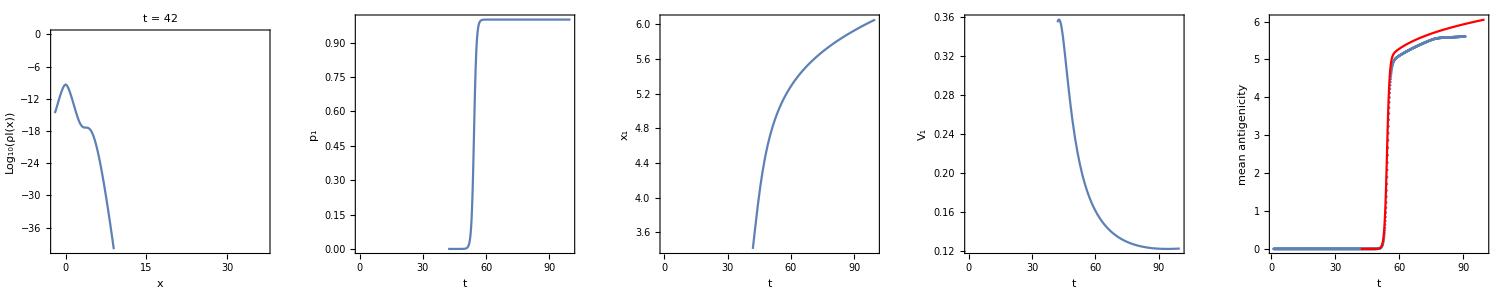

t0 = 43 xc= 2.79515

Sum(I(x),x<xc)= 9.48741×10^-10	Sum(I(x),x>xc)= 8.49688×10^-17

p0 = 1.	p1 = 8.95595×10^-8

E[x|x<xc] = 6.72099×10^-7	E[x|x>xc] = 3.62186

V[x|x<xc] = 0.0984692	V[x|x>xc] = 0.415212

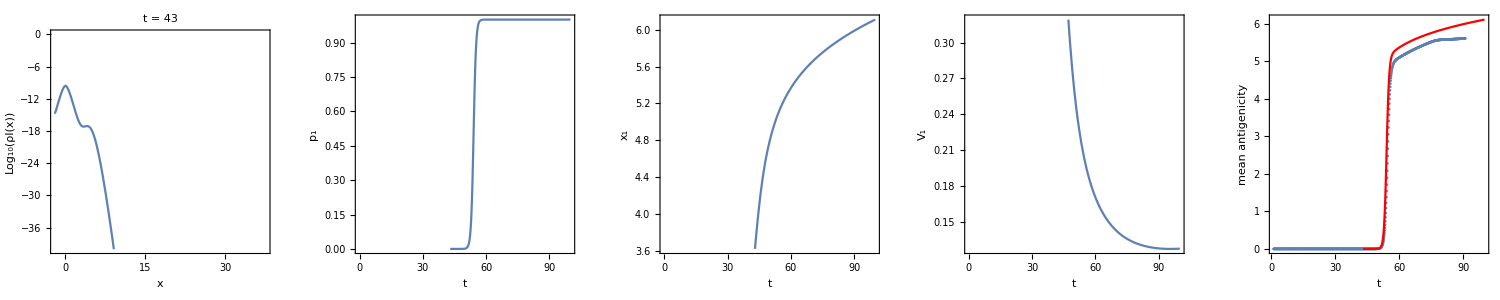

t0 = 44 xc= 2.79515

Sum(I(x),x<xc)= 5.63656×10^-10	Sum(I(x),x>xc)= 1.42952×10^-16

p0 = 1.	p1 = 2.53615×10^-7

E[x|x<xc] = 9.76492×10^-7	E[x|x>xc] = 3.85019

V[x|x<xc] = 0.101405	V[x|x>xc] = 0.419005

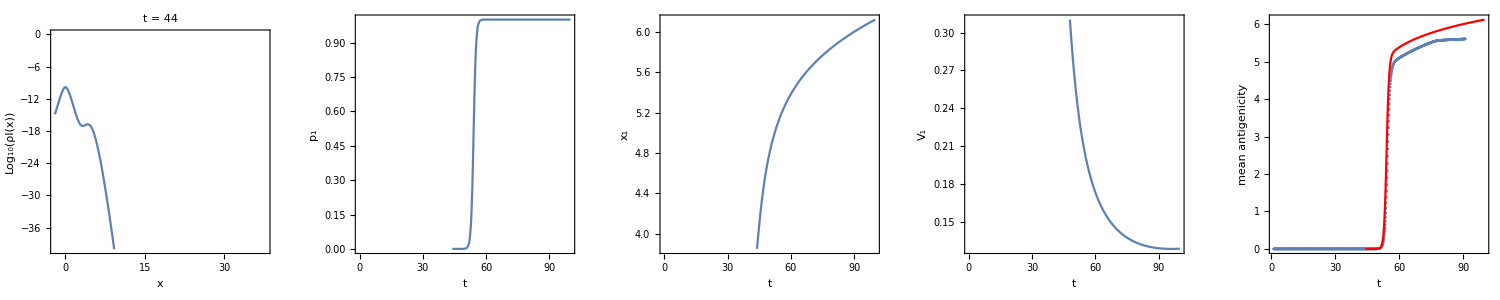

t0 = 45 xc= 2.79515

Sum(I(x),x<xc)= 3.34908×10^-10	Sum(I(x),x>xc)= 2.70928×10^-16

p0 = 0.999999	p1 = 8.08962×10^-7

E[x|x<xc] = 1.41416×10^-6	E[x|x>xc] = 4.06191

V[x|x<xc] = 0.1044	V[x|x>xc] = 0.371224

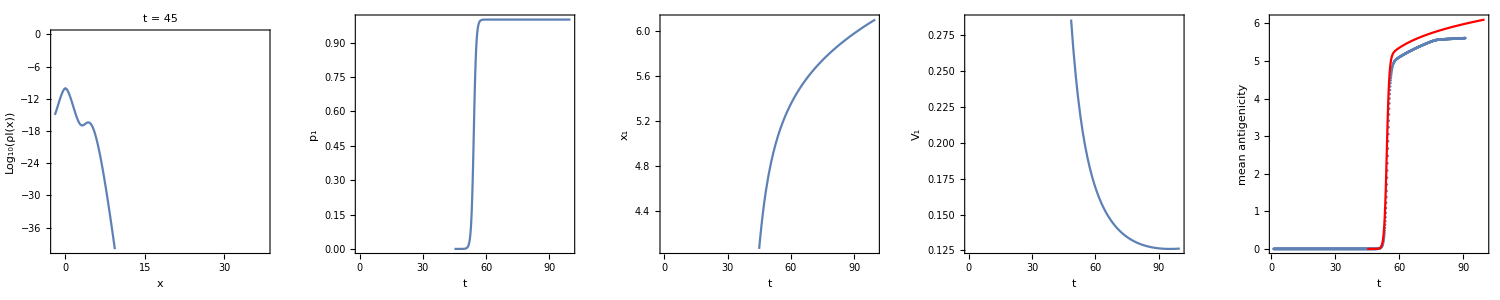

t0 = 46 xc= 2.79515

Sum(I(x),x<xc)= 1.99014×10^-10	Sum(I(x),x>xc)= 5.68802×10^-16

p0 = 0.999997	p1 = 2.85809×10^-6

E[x|x<xc] = 2.04225×10^-6	E[x|x>xc] = 4.23684

V[x|x<xc] = 0.107457	V[x|x>xc] = 0.304795

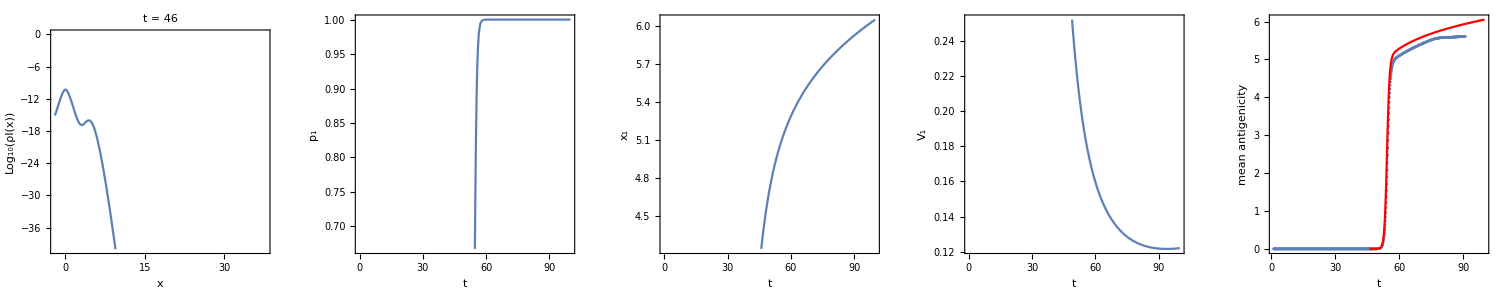

t0 = 47 xc= 2.79515

Sum(I(x),x<xc)= 1.18274×10^-10	Sum(I(x),x>xc)= 1.29317×10^-15

p0 = 0.999989	p1 = 0.0000109336

E[x|x<xc] = 2.94238×10^-6	E[x|x>xc] = 4.37336

V[x|x<xc] = 0.110581	V[x|x>xc] = 0.246713

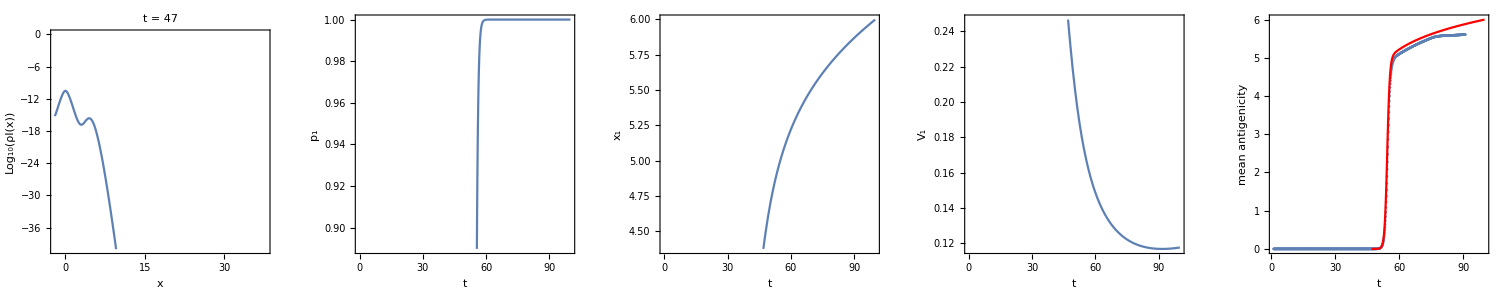

t0 = 48 xc= 2.79515

Sum(I(x),x<xc)= 7.02983×10^-11	Sum(I(x),x>xc)= 3.12038×10^-15

p0 = 0.999956	p1 = 0.0000443858

E[x|x<xc] = 4.2306×10^-6	E[x|x>xc] = 4.47975

V[x|x<xc] = 0.113776	V[x|x>xc] = 0.20548

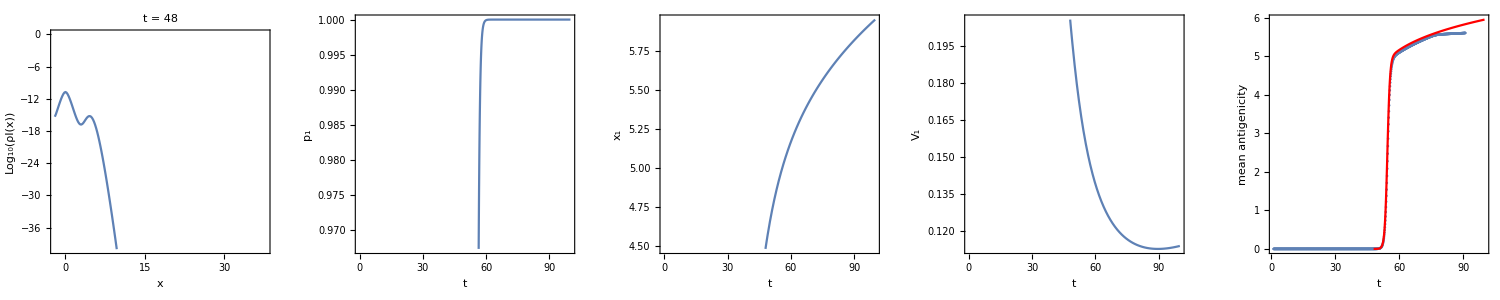

t0 = 49 xc= 2.79515

Sum(I(x),x<xc)= 4.17878×10^-11	Sum(I(x),x>xc)= 7.87497×10^-15

p0 = 0.999812	p1 = 0.000188416

E[x|x<xc] = 6.07327×10^-6	E[x|x>xc] = 4.56547

V[x|x<xc] = 0.117048	V[x|x>xc] = 0.178797

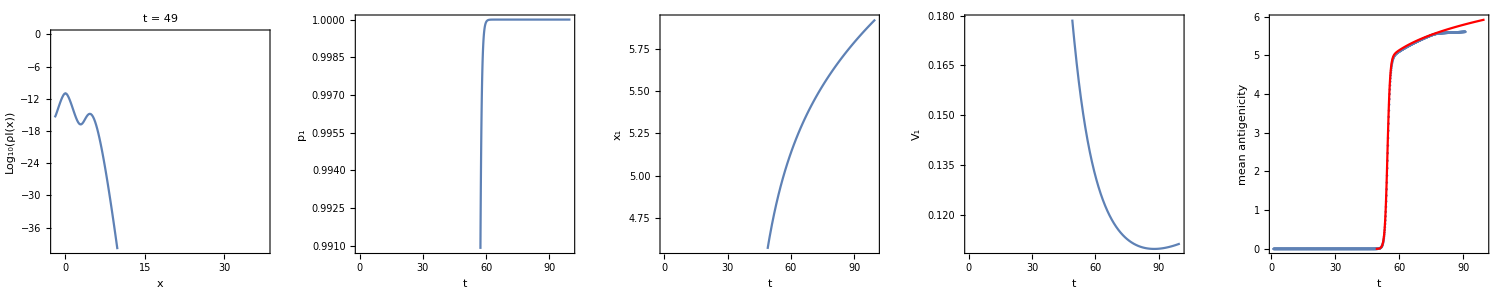

t0 = 50 xc= 2.79515

Sum(I(x),x<xc)= 2.48431×10^-11	Sum(I(x),x>xc)= 2.05834×10^-14

p0 = 0.999172	p1 = 0.00082785

E[x|x<xc] = 8.70822×10^-6	E[x|x>xc] = 4.63759

V[x|x<xc] = 0.120401	V[x|x>xc] = 0.161923

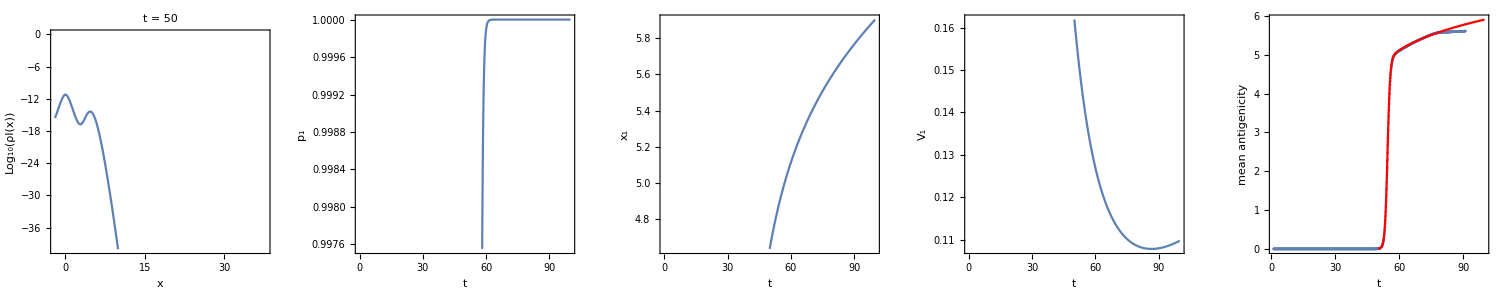

t0 = 51 xc= 2.79515

Sum(I(x),x<xc)= 1.47712×10^-11	Sum(I(x),x>xc)= 5.53599×10^-14

p0 = 0.996266	p1 = 0.00373384

E[x|x<xc] = 0.0000124772	E[x|x>xc] = 4.70065

V[x|x<xc] = 0.123844	V[x|x>xc] = 0.151034

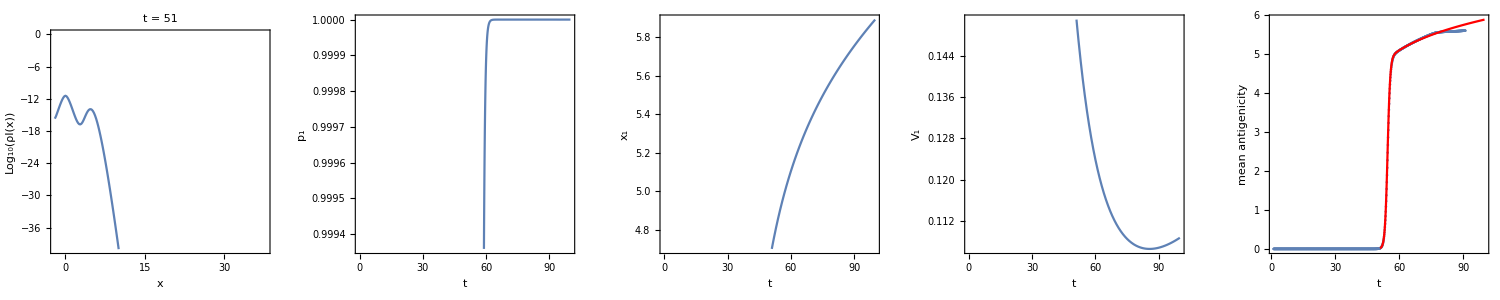

```mathematica
prediction={};
Do[
i0=i0ser⟦i⟧;
t0=timeTR[[i0]];
(* Susceptibility profile at t = t0 *)
grf0=ListLinePlot[Transpose[{xval,Log10[ρI⟦i0⟧]}],PlotRange->{-40,0},PlotLabel->"t = "<>ToString[t0],Frame->True,FrameLabel->{"x","Log_10(ρI(x))"},ImageSize->250];

(* Divide the antigenicity between two antigenicity groups,those with x<xc and those with x>xc *)
ic=Select[xval,#<xc&]//Length;
(* infected density distribution and antigeniciy traits for x<xc group *)
ρI0=Take[ρI⟦i0⟧,ic];
xval0=Take[xval,ic];
(* infected density distribution and antigeniciy traits for x>xc group *)
ρI1=Take[ρI⟦i0⟧,{ic+1,Length[xval]}];
xval1=Take[xval,{ic+1,Length[xval]}];
(* total infected densities of two groups *)
I0=ρI0//Total;
I1=ρI1//Total;
(* relative proportion of two groups in infected population *)
(* THE INITIAL CONDITION FOR THE 0TH ORDER OMD *)
p0=I0/(I0+I1);
p1=I1/(I0+I1);
(* mean antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 1ST ORDER OMD *)
(* inner product of trait vector and density vector *)
ex0=xval0.ρI0/I0;
ex1=xval1.ρI1/I1;
(* variance of antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 2ND ORDER OMD *)
V0=((xval0-ex0)^2).ρI0/I0;
V1=((xval1-ex1)^2).ρI1/I1;
Print["t0 = ",t0, " xc= ",xc];
Print["Sum(I(x),x<xc)= ",I0, "\tSum(I(x),x>xc)= ",I1];
Print["p0 = ",p0,"\tp1 = ",p1];
Print["E[x|x<xc] = ",ex0,"\tE[x|x>xc] = ",ex1];
Print["V[x|x<xc] = ",V0,"\tV[x|x>xc] = ",V1];

(* Integrating OMD for the second epidemic outbreak
and Compare with simulation results *)
tend=100;
Clear[t,P,M,V];
ser=NDSolve[{
P'[t]==β (s[M[t]]-s[ex0])P[t](1-P[t]),
M'[t]==β s'[M[t]]V[t],
V'[t]==β s''[M[t]]V[t]^2+2𝒟,
P[t0]==p1,
M[t0]==ex1,
V[t0]==V1},
{P,M,V},{t,t0,tend}];
(* Frequency of morph 1 *)
grf1=Plot[P[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","p_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
(* Mean antigenicity of morph 1 *)
grf2=Plot[M[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","x_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
(* Variance in morph 1 *)
grf3=Plot[V[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","V_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
grf4=Show[
ListPlot[Take[Transpose[{tval,ex}],900],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}],
Plot[((1-P[t])ex0+P[t]M[t])/.ser,{t,t0,tend},PlotRange->All,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"t","mean antigenicity"},Axes->None,ImageSize->250
];
GraphicsRow[{grf0,grf1,grf2,grf3,grf4},ImageSize->1500]//Print;
AppendTo[prediction,{ser,t0}],
{i,Length[i0ser]}
]
```

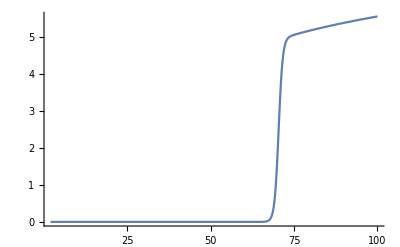

```mathematica
{ser0,τ0}=prediction⟦1⟧;
Plot[(1-P[t])ex0+P[t]M[t]/.ser0,{t,τ0,tend}]
```

```mathematica
n=Length[i0ser];
Clear[F,τ]
Do[
{ser0,τ0}=prediction⟦i⟧;
Subscript[F, i][t_]=(1-P[t])ex0+P[t]M[t]/.ser0;
Subscript[τ, i]=τ0,
{i,n}]
```

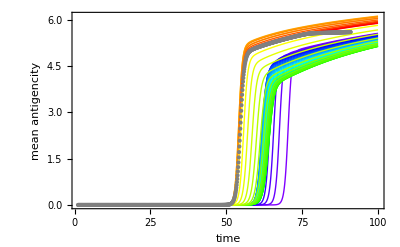

```mathematica
Show[
Table[
Plot[Subscript[F, i][t],{t,Subscript[τ, i],tend},PlotStyle->{Hue[0.75(1-(i-1)/(n-1))],AbsoluteThickness[1]},Frame->True,FrameLabel->{"time", "mean antigencity"}],
{i,n}],
ListPlot[Take[Transpose[{tval,ex}],900],PlotRange->All,PlotStyle->{Thick,Gray}],
PlotRange->All]
```

### Best timing to start OMD prediction

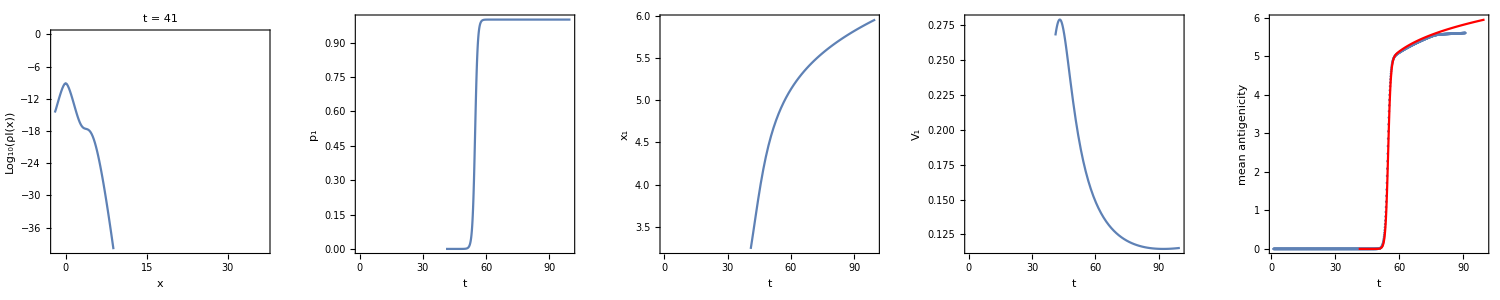

```mathematica
tend=100;
i0=40;
{serBest,t0Best}=prediction[[i0]];
grf0=ListLinePlot[Transpose[{xval,Log10[ρI⟦i0⟧]}],PlotRange->{-40,0},PlotLabel->"t = "<>ToString[t0Best],Frame->True,FrameLabel->{"x","Log_10(ρI(x))"},ImageSize->250];
(* Frequency of morph 1 *)
grf1=Plot[P[t]/.serBest,{t,t0Best,tend},Frame->True,FrameLabel->{"t","p_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
(* Mean antigenicity of morph 1 *)
grf2=Plot[M[t]/.serBest,{t,t0Best,tend},Frame->True,FrameLabel->{"t","x_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
(* Variance in morph 1 *)
grf3=Plot[V[t]/.serBest,{t,t0Best,tend},Frame->True,FrameLabel->{"t","V_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}];
grf4=Show[
ListPlot[Take[Transpose[{tval,ex}],900],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}],
Plot[((1-P[t])ex0+P[t]M[t])/.serBest,{t,t0Best,tend},PlotRange->All,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"t","mean antigenicity"},Axes->None,ImageSize->250
];
GraphicsRow[{grf0,grf1,grf2,grf3,grf4},ImageSize->1500]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fig/LogarithmicViralDensityAtT0.eps",grf0]
Export["fig/LogarithmicViralDensityAtT0.pdf",grf0]
```

fig/LogarithmicViralDensityAtT0.eps

fig/LogarithmicViralDensityAtT0.pdf

### Comparing inflection point of mean antigenicity

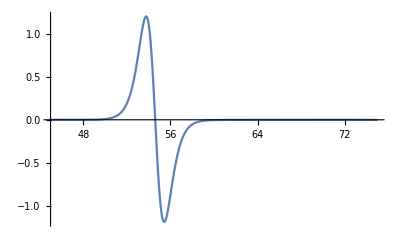

54.8718

54.6061

```mathematica
data=Take[Transpose[{tval,ex}],900];
f=Interpolation[data,InterpolationOrder->5, Method->"Spline"];
Plot[f''[t],{t,45,75},PlotRange->All]
ttest=t/.FindRoot[f[t]==3,{t,55}]
tMC=t/.FindRoot[f''[t]==0,{t,ttest}]
```

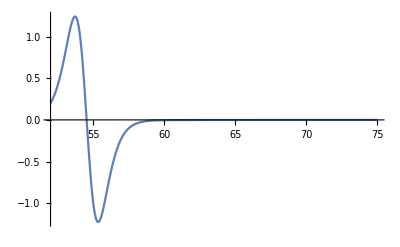

54.8013

{t→54.5398}

```mathematica
Clear[f]
{ser0,τ0}=prediction//Last;
f[t_]=(1-P[t])ex0+P[t]M[t]/.ser0;
Plot[f''[t],{t,52,75},PlotRange->All]
ttest=t/.FindRoot[f[t]==3,{t,55}]
FindRoot[f''[t]==0,{t,ttest}]
```

```mathematica
InflectionPoints={};
tc=55;
Do[
{ser0,τ0}=prediction⟦i⟧;
f[t_]=(1-P[t])ex0+P[t]M[t]/.ser0;
ttest=t/.FindRoot[f[t]==2.5,{t,tc}];
tc=t/.FindRoot[f''[t]==0,{t,ttest}];
Print[{τ0,tc}];
AppendTo[InflectionPoints,{τ0,tc}],
{i,Length[i0ser],1,-1}]
```

{51,54.5398}

{50,54.5185}

{49,54.4913}

{48,54.4511}

{47,54.388}

{46,54.2933}

{45,54.1776}

{44,54.0829}

{43,54.0845}

{42,54.2862}

{41,54.8047}

{40,55.7197}

{39,56.9982}

{38,58.4753}

{37,59.9197}

{36,61.1582}

{35,62.1275}

{34,62.8382}

{33,63.3249}

{32,63.6504}

{31,63.8557}

{30,63.9534}

{29,63.9797}

{28,63.9437}

{27,63.8611}

{26,63.7644}

{25,63.6141}

{24,63.4639}

{23,63.2888}

{22,63.118}

{21,62.9109}

{20,62.733}

{19,62.5462}

{18,62.3629}

{17,62.2066}

{16,62.0005}

{15,61.8725}

{14,61.7627}

{13,61.6941}

{12,61.67}

{11,61.6927}

{10,61.7826}

{9,61.9685}

{8,62.2373}

{7,62.6838}

{6,63.3131}

{5,64.2534}

{4,65.6003}

{3,67.5115}

InterpolatingFunction::dmval: Input value {100.435} lies outside the range of data in the interpolating function. Extrapolation will be used.

{2,70.3772}

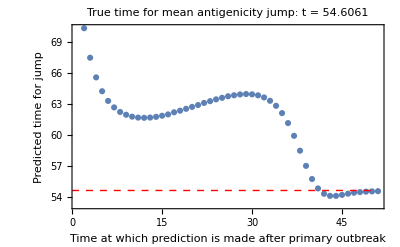

```mathematica
Show[
ListPlot[InflectionPoints,PlotRange->All,Frame->True,FrameLabel->{"Time at which prediction is made after primary outbreak","Predicted time for jump"},PlotLabel->"True time for mean antigenicity jump: t = "<>ToString[tMC]],
Graphics[{Dashed,Red,Line[{{0,tMC},{50,tMC}}]}]
]
```

### Weighted logarithmic odds ratio (KL divergence-like) (revised)

#### Kullback - Leibler divergence from Q to P

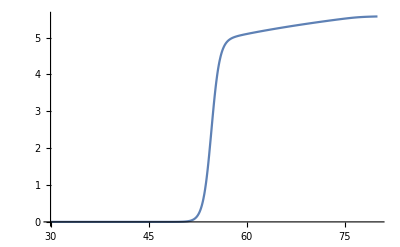

```mathematica
data=Take[Transpose[{tval,ex}],900];
𝒬=Interpolation[data,InterpolationOrder->5, Method->"Spline"];
ts=30;
te=80;
Plot[𝒬[t],{t,ts,te}]
```

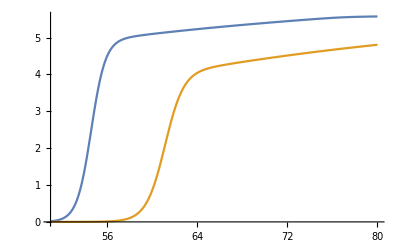

154.448

```mathematica
{ser0,τ0}=prediction⟦35⟧;
𝒫[t_]=(1-P[t])ex0+P[t]M[t]/.ser0⟦1⟧;
ts=51;
te=80;
Plot[{𝒬[t],𝒫[t]},{t,ts,te}]
KL=NIntegrate[𝒬[t]Log[𝒬[t]/𝒫[t]],{t,ts,te}]//Chop
```

```mathematica
KLdivergence={};
Do[
{ser0,τ0}=prediction⟦i⟧;
𝒫[t_]=(1-P[t])ex0+P[t]M[t]/.ser0⟦1⟧;
ts=51;
te=80;
KL=1/(te-ts)NIntegrate[𝒬[t]Log[𝒬[t]/𝒫[t]],{t,ts,te}]//Chop;
Print[{τ0,KL}];
AppendTo[KLdivergence,{τ0,KL}],
{i,Length[i0ser]}]
```

{2,26.9251}

{3,20.0234}

{4,15.4492}

{5,12.264}

{6,10.1131}

{7,8.73518}

{8,7.79851}

{9,7.24012}

{10,6.85013}

{11,6.6366}

{12,6.53877}

{13,6.51745}

{14,6.56631}

{15,6.67933}

{16,6.81942}

{17,7.08569}

{18,7.26704}

{19,7.49206}

{20,7.72235}

{21,7.93674}

{22,8.20292}

{23,8.40724}

{24,8.62208}

{25,8.79723}

{26,8.97953}

{27,9.07409}

{28,9.15665}

{29,9.17223}

{30,9.09889}

{31,8.92937}

{32,8.61179}

{33,8.14184}

{34,7.47309}

{35,6.53597}

{36,5.32578}

{37,3.89562}

{38,2.42484}

{39,1.20213}

{40,0.417059}

{41,0.00271363}

{42,-0.2014}

{43,-0.290527}

{44,-0.304421}

{45,-0.266485}

{46,-0.201056}

{47,-0.133184}

{48,-0.079097}

{49,-0.0425099}

{50,-0.0198587}

{51,-0.00620592}

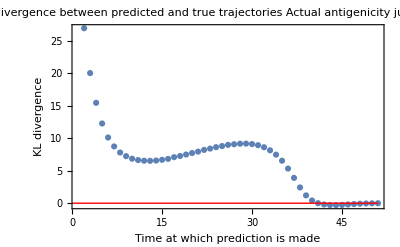

```mathematica
grfKL=Show[
ListPlot[KLdivergence,PlotRange->All,Frame->True,FrameLabel->{"Time at which prediction is made","KL divergence"},PlotLabel->"Kullback-Leibler divergence between predicted and true trajectories\nActual antigenicity jump occured at t = "<>ToString[tMC]],
Graphics[{Red,Line[{{0,0},{51,0}}]}]
]
```

### L2 norm

```mathematica
data=Take[Transpose[{tval,ex}],900];
𝒬=Interpolation[data,InterpolationOrder->5, Method->"Spline"];
ts=30;
te=80;
Plot[𝒬[t],{t,ts,te}]
```

-Graphics-

```mathematica
{ser0,τ0}=prediction⟦35⟧;
𝒫[t_]=(1-P[t])ex0+P[t]M[t]/.ser0⟦1⟧;
ts=51;
te=80;
Plot[{𝒬[t],𝒫[t]},{t,ts,te}]
NIntegrate[(𝒫[t]-𝒬[t])^2,{t,ts,te}]//Sqrt[#]&
```

-Graphics-

12.3644

```mathematica
L2norm={};
Do[
{ser0,τ0}=prediction⟦i⟧;
𝒫[t_]=(1-P[t])ex0+P[t]M[t]/.ser0⟦1⟧;
ts=51;
te=80;
dl2=1/(te-ts)NIntegrate[(𝒫[t]-𝒬[t])^2,{t,ts,te}];
diffPQ=1/(te-ts)NIntegrate[𝒬[t]-𝒫[t],{t,ts,te}];
Print[{τ0,dl2,diffPQ}];
AppendTo[L2norm,{τ0,dl2,diffPQ}],
{i,Length[i0ser]}]
```

{2,13.5829,2.95747}

{3,10.775,2.48286}

{4,8.95693,2.17873}

{5,7.70623,1.97366}

{6,6.85346,1.83861}

{7,6.29681,1.7558}

{8,5.9133,1.70371}

{9,5.69495,1.68061}

{10,5.55356,1.67113}

{11,5.50057,1.67696}

{12,5.50942,1.69337}

{13,5.56149,1.71702}

{14,5.65432,1.74735}

{15,5.78483,1.78368}

{16,5.9328,1.82255}

{17,6.15027,1.87227}

{18,6.32451,1.91452}

{19,6.52309,1.96012}

{20,6.72517,2.00568}

{21,6.91928,2.04931}

{22,7.13894,2.0962}

{23,7.32582,2.13717}

{24,7.5153,2.17765}

{25,7.68112,2.21349}

{26,7.84464,2.24786}

{27,7.95733,2.27319}

{28,8.05339,2.29448}

{29,8.10226,2.30678}

{30,8.08815,2.3072}

{31,8.00033,2.2934}

{32,7.80297,2.25876}

{33,7.47962,2.19882}

{34,6.98735,2.1038}

{35,6.26309,1.95871}

{36,5.27167,1.74967}

{37,4.01123,1.46465}

{38,2.57566,1.10578}

{39,1.2161,0.703787}

{40,0.304931,0.315802}

{41,0.0101369,-0.000374722}

{42,0.0604227,-0.211298}

{43,0.143016,-0.314905}

{44,0.152964,-0.329822}

{45,0.110134,-0.284354}

{46,0.0597178,-0.210707}

{47,0.0263265,-0.13759}

{48,0.0104079,-0.0810013}

{49,0.00420942,-0.0433772}

{50,0.00198361,-0.0202944}

{51,0.00112191,-0.00643706}

```mathematica
{tau,DL2,DIFF}=Transpose[L2norm];
```

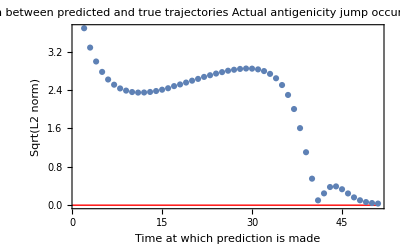

```mathematica
grfL2Sqrt=Show[
ListPlot[Transpose[{tau,Sqrt[DL2]}],PlotRange->All,Frame->True,FrameLabel->{"Time at which prediction is made","Sqrt(L2 norm)"},PlotLabel->"L2 norm between predicted and true trajectories\nActual antigenicity jump occured at t = "<>ToString[tMC]],
Graphics[{Red,Line[{{0,0},{51,0}}]}]
]
```

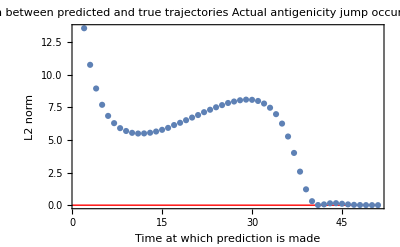

```mathematica
grfL2=Show[
ListPlot[Transpose[{tau,DL2}],PlotRange->All,Frame->True,FrameLabel->{"Time at which prediction is made","L2 norm"},PlotLabel->"L2 norm between predicted and true trajectories\nActual antigenicity jump occured at t = "<>ToString[tMC]],
Graphics[{Red,Line[{{0,0},{51,0}}]}]
]
```

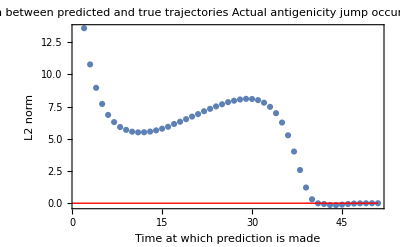

```mathematica
grfL2Modified=Show[
ListPlot[Transpose[{tau,Sign[DIFF]DL2}],PlotRange->All,Frame->True,FrameLabel->{"Time at which prediction is made","L2 norm"},PlotLabel->"L2 norm between predicted and true trajectories\nActual antigenicity jump occured at t = "<>ToString[tMC]],
Graphics[{Red,Line[{{0,0},{51,0}}]}]
]
```

### Save to file

```mathematica
Export["fig/JumpPredictionAccuracy-L2.eps",grfL2];
Export["fig/JumpPredictionAccuracy-L2.pdf",grfL2];
```

```mathematica
Export["fig/JumpPredictionAccuracy-KL.eps",grfKL];
Export["fig/JumpPredictionAccuracy-KL.pdf",grfKL];
```